```mathematica
$ProcessorCount
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

2

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
Needs["CCompilerDriver`GenericCCompiler`"]
$CCompiler={"Name"->"Visual Studio","Compiler"->CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,"CompilerInstallation"->"C:\\Program Files (x86)\\Microsoft Visual Studio\\2017\\Community","CompilerName"->Automatic};
<<CompiledFunctionTools`(*позволяет смотреть "код"*)
```

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[235,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[10^(-3)/lc,MachinePrecision];(*период ондулятора 10 мкм*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=4;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=40;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
```

```mathematica
mpp=SetPrecision[938.27 10^6,MachinePrecision];(*масса протона в эВ*)
Mmol=18 12+19+14;(*относительная молярная масса C18H19N*)
Zn=18 6+19+7;(*число электронов в молекуле*)
nmm=5.60958 10^(32)/(mpp Mmol);(*концентрация молекул при плотности массы 1 g/cm^3 в 1/cm^3*)
ωp=Sqrt[4 Pi α Zn nmm lc^3];(*плазменная частота в естественных единицах*)
With[{ωp=ωp},
ϵpp=Compile[{{k0,_Real}},2.4,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*перпендикулярная диэлектрическая проницаемость. должно считаться точно*)
ϵpl=Compile[{{k0,_Real}},2.9,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*параллельная диэлектрическая проницаемость. должно считаться точно*)
dec=Compile[{{k0,_Real}},(ϵpl[k0]-ϵpp[k0])/ϵpp[k0],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"]];(*анизотропия. должно считаться точно*)
Print["Волновой вектор холестерика q: ",qc mee, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lc 10^4, " мкм"]
Print["Плазменная частота: ",ωp mee," эВ,  ",2.42 10^(14) ωp mee," Гц"]
Module[{xx=83/mee},(*предполагаемая энергия фотона*)
Print["Анизотропия de: ",dec[xx]];
Print["Параметр ВКБ: ", (dec[xx] ϵpp[xx]^(1/2) xx/(4 qc))^2]]
```

Волновой вектор холестерика q: 0.619667 эВ

Толщина пластины холестерика Lz: 40. мкм

Плазменная частота: 21.0523 эВ,  5.09467×10^15 Гц

Анизотропия de: 0.208333

Параметр ВКБ: 116.802

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0.;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]:={0.,0.,zo+βp t};
rtn=Compile[{{t,_Real}},Evaluate[rt[t]],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*далее нужно исправить вызов этой функции*)
v[t_]:={0,0,βp};
vn=Compile[{{t,_Real}},Evaluate[v[t]],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
xo=rtn[0][[1]];yo=rtn[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rtn[tfin];
vxf=0.;vyf=0.;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp=Compile[{{t,_Real}},Evaluate[rt[t].ep],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
xm=Compile[{{t,_Real}},Evaluate[rt[t].em],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
x3=Compile[{{t,_Real}},Evaluate[rt[t].e3],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
x0=Compile[{{t,_Real}},t,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->"Speed",CompilationTarget->"C"];  (*c=1*)
vp=Compile[{{t,_Real}},Evaluate[v[t].ep],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
vm=Compile[{{t,_Real}},Evaluate[v[t].em],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
v3=Compile[{{t,_Real}},Evaluate[v[t].e3],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
```

```mathematica
pp=10;(*2p+1-волновое приближение*)
```

```mathematica
aaa[n_]:={{k0s-kp^2-(qn+2 n)^2+de (k0s-kp^2/2)/2,de (k0s-kp^2/2)/2},{de (k0s-kp^2/2)/2,k0s-kp^2-(qn+2 n-2)^2+de (k0s-kp^2/2)/2}};
bbb[n_]:=-kp^2 de/4 {{1,1},{0,0}};
ccc[n_]:=-kp^2 de/4 {{0,0},{1,1}};
```

```mathematica
mmi[p_]:=Module[{mm1,i},
mm1=ConstantArray[0,{2p+1,2p+1}];
Do[
mm1[[i,i]]=aaa[p-i+1];
If[i<2p+1,mm1[[i,i+1]]=ccc[p-i+1]];
If[i>1,mm1[[i,i-1]]=bbb[p-i+1]];
,{i,1,2 p+1}];
Drop[Drop[ArrayFlatten[mm1],-1,-1],1,1]]
```

```mathematica
If[FailureQ[FindFile[NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"]],
dspp=If[pp≤10,Collect[Det[mmi[pp]],qn,Simplify],Collect[Det[mmi[pp]],qn]];(*дисперсионнный определитель. если есть, то загружается из файла*)
Put[dspp,NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"];,
dspp=Get[NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"];]

mmieq=mmi[pp];(*матрица уравнения*)
```

```mathematica
dsp[k0s1_?NumberQ,kp1_?NumberQ,de1_?NumberQ,qn1_]=dspp/.{k0s->k0s1,kp->kp1,de->de1,qn->qn1};
meq=Compile[{{k0s1,_Real},{kp1,_Real},{de1,_Real},{qn1,_Complex}},Evaluate[mmieq/.{k0s->k0s1,kp->kp1,de->de1,qn->qn1}],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*функции для определителя и матрицы*)
```

```mathematica
PolynomialQ[dspp,qn]
```

True

```mathematica
Clear[ChoiceMainBranch,Branches]
```

```mathematica
ChoiceMainBranch=Compile[{{p,_Integer},{k0s,_Real},{kp,_Real},{de,_Real},{rts,_Complex,1}},Module[{i,j,k,nmax,ff,rtss,mm1,mm1n,eigv,eigv1},
Do[
rtss=rts[[i]];
mm1n=meq[k0s,kp,de,rtss];
eigv=NullSpace[mm1n];
Do[
eigv1=eigv[[k]]/Norm[eigv[[k]]];
nmax=Abs[eigv1[[2 p]]]^2+Abs[eigv1[[2 p+1]]]^2;
If[Abs[eigv1[[1]]]^2<nmax,
j=1;(*счетчик*)
While[(j<p)&&((Abs[eigv1[[2 j+1]]]^2+Abs[eigv1[[2 j]]]^2)<nmax),j++];
If[j==p,
j++;
While[(j<2 p)&&((Abs[eigv1[[2 j+1]]]^2+Abs[eigv1[[2 j]]]^2)<nmax),j++];
If[j==2 p,
If[Abs[eigv1[[4 p]]]^2<nmax,
ff=True,(*флаг для основой ветви*)
ff=False],

ff=False],
ff=False];
If[ff==True,
Sow[Append[eigv1,rtss]]]](*записываем в стек (СВ,СЗ), СЗ -- последний элемент 4p+1*);
,{k,1,Length[eigv]}];
,{i,1,Length[rts]}];
],{{NullSpace[_],_Complex,2},{Length[_],_Integer},{Norm[_],_Real},{meq[_],_Complex,2}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];
(*"InlineCompiledFunctions"->True,*)
Branches[p_?IntegerQ,k0s_?NumberQ,kp_?NumberQ,de_?NumberQ]:=
Module[{rts,ddsp,q1},
ddsp=dsp[k0s,kp,de,q1];
rts=q1/.{ToRules[NRoots[ddsp==0,q1,PrecisionGoal->30]]};
Last[Reap[ChoiceMainBranch[p,k0s,kp,de,rts]]][[1]]

];
```

```mathematica
(*Branches возвращает список {{компСВ, СЗ},{компСВ, СЗ},...}*)
```

```mathematica
SetSharedFunction[ParallelSow]
ParallelSow[ex_]:=Sow[ex];
```

```mathematica
DisperMain[p_?IntegerQ,de1_?NumberQ,kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];
dee=SetPrecision[de1,Infinity];(*точные числа*)
Last[Reap[
Parallelize[
Do[Module[{llb,i},
llb=Branches[p,k0^2,kpe,dee];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]]][[1]]];
```

```mathematica
DisperSimpl[de1_?NumberQ,kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];
dee=SetPrecision[de1,Infinity];(*точные числа*)
Last[Reap[
Parallelize[
Do[Module[{rts1,rts2,i,dssp,q1},
dssp=dsp[k0^2,kpe,dee,q1];
rts1=q1/.{ToRules[NRoots[dssp==0,q1,PrecisionGoal->30]]};
rts2=Sort[Select[rts1,(Chop[#]∈Reals)&]];(*оставляем только вещественные корни*)
Do[ParallelSow[{Re[rts2[[i]]],k0}],{i,1,Length[rts2]}]]
,{k0,k0ie,k0fe,dk0e}]]]][[1]]];
```

```mathematica
With[{qc=qc,Lz=Lz},CoeffLinComb=Compile[{{s,_Integer},{k00,_Real},{k0,_Real},{k0s,_Real},{kp,_Real},{ϕ,_Real},{rff,_Complex},{n3,_Real},{k3b,_Real},{de,_Real},{p,_Integer},{branchs,_Complex,2},{numb,_Integer}},Module[{ii,r,n3i,u0t,umLt,h0i,t0l,tpi,tm,gv,ach,al},

n3i=1/n3;

r=1/rff^2;(*общие фазовые множители*)
t0l=Exp[-I k00 n3 Lz];

u0t=Table[Module[{tf,pf,ap,am,mrap,ram,l},(*транспонированная матрица U(0)*)
pf=branchs[[ii,4 p+1]];(*импульс закона дисперсии*)
tf=Exp[-I pf ϕ];(*фазовые множители, зависящие от ветви*)
ap=0.+I 0.;
am=0.+I 0.;
mrap=0.+I 0.;
ram=0.+I 0.;
Do[Module[{apl,aml},
apl=branchs[[ii,2 l]];
aml=branchs[[ii,2 l-1]];
ap+=r^(p-l) apl;
am+=r^(p-l) aml;
mrap+=r^(p-l) (apl+kp^2/(2 k3b^2) (apl+aml)) (pf+2 (p-l));
ram+=r^(p-l) (aml+kp^2/(2 k3b^2) (apl+aml)) (pf+2 (p-l));]
,{l,1,2 p}];
{tf ap,tf am,tf mrap,tf ram}]
,{ii,1,numb}];

umLt=Table[Module[{tfl},(*транспонированная матрица U(-L). предполагаем целое число периодов*)
tfl=Exp[-I branchs[[ii,4 p+1]] qc Lz];
tfl u0t[[ii]]]
,{ii,1,numb}];

h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
(*tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};*)

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=LinearSolve[Transpose[u0t],gv];

(*ach=Check[LinearSolve[Transpose[u0t],gv],ConstantArray[0.+I 0.,numb],{LinearSolve::nosol}];*)(*коэфф. ЛК в среде. для несовместной системы выдает трив. ответ. {Check[_,_,_],_Complex,1} {LinearSolve[_,_],_Complex,1} "InlineCompiledFunctions"->True*)
al=tpi.h0i.Transpose[umLt].ach;

Join[ach,al]],{{LinearSolve[_,_],_Complex,1} ,{Join[_],_Complex,1}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];(*выдает ответ в виде списка (ach,al)*)
```

```mathematica
ModeFun=Compile[{{tetb,_Real},{kp,_Real},{k3b,_Real},{rftet,_Complex},{p,_Integer},{branchs,_Complex,2},{numb,_Integer},{achl,_Complex,1}},Module[{ap,am,a3,bi},

ap=0.+I 0.;(*начальные значения*)
am=0.+I 0.;
a3=0.+I 0.;

Do[Module[{pf,tf},
pf=branchs[[ii,4 p+1]];(*импульс закона дисперсии*)
tf=Exp[I pf tetb];(*фазовые множители, зависящие от ветви*)
bi=achl[[ii]];(*множитель линейной комбинации мод в среде*)
Do[Module[{apl,aml},
apl=branchs[[ii,2 l]];
aml=branchs[[ii,2 l-1]];
ap+=rftet^(p-l) apl;
am+=rftet^(p-l) aml;
a3+=rftet^(p-l) (apl+aml) (pf+2 (p-l))(*без общего множителя*);
],{l,1,2 p}];
ap=bi tf ap;
am=bi tf am;
a3=bi tf a3;
],{ii,1,numb}];
a3=-kp/(2 k3b^2) a3; (*восстанавливаем общий множитель*)

{ap,am,a3}],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];(*ответ в виде списка без общего экспоненциального фазового множителя "InlineCompiledFunctions"->True*)
```

```mathematica
With[{qc=qc},InteGrand=Compile[{{t,_Real},{k00,_Real},{kpp,_Complex},{kpm,_Complex},{kp,_Real},{ϕ,_Real},{k3b,_Real},{achli,_Complex,1},{p,_Integer},{branchs,_Complex,2},{numb,_Integer}},Module[{rftet,arl,tet},

tet=qc x3[t]-ϕ;
rftet=Exp[2 I tet];(*фазовый множитель*)

arl=ModeFun[tet,kp,k3b,rftet,p,branchs,numb,achli];(*значения модовых функций*)

(1/2 (vp[t] arl[[2]]+vm[t] arl[[1]])+v3[t] arl[[3]]) Exp[-I k00 x0[t]+I (kpp xm[t]+kpm xp[t])/2]
],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];
```

```mathematica
(*fps=Compile[{{ss,_Integer},{cffs,_Real},{sffs,_Real},{npss,_Real},{n3ss,_Real}},{cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True},CompilationTarget->"C"];
fms=Compile[{{ss,_Integer},{cffs,_Real},{sffs,_Real},{npss,_Real},{n3ss,_Real}},{-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True},CompilationTarget->"C"];*)
fps[ss_,cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_,cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
(*fps[1,cff,sff,nps,n3s].{vx01,vy01,vz01}//FullSimplify
fps[-1,cff,sff,nps,n3s].{vx01,vy01,vz01}//FullSimplify
fms[1,cff,sff,nps,n3s].{vx01,vy01,vz01}//FullSimplify
fms[-1,cff,sff,nps,n3s].{vx01,vy01,vz01}//FullSimplify
fps[s1,cff,sff,nps,n3s].{vxf1,vyf1,vzf1}//FullSimplify
(cff n3s vx01-ⅈ sff vx01+ⅈ cff vy01+n3s sff vy01-nps vz01)/(√2)
(cff n3s vx01+ⅈ sff vx01-ⅈ cff vy01+n3s sff vy01-nps vz01)/(√2)
-(cff n3s vx01+ⅈ sff vx01-ⅈ cff vy01+n3s sff vy01+nps vz01)/(√2)
-(cff n3s vx01-ⅈ sff vx01+ⅈ cff vy01+n3s sff vy01+nps vz01)/(√2)
(cff n3s vxf1-ⅈ s1 sff vxf1+ⅈ cff s1 vyf1+n3s sff vyf1-nps vzf1)/(√2)*)
```

```mathematica
With[{xo=xo,yo=yo,zo=zo,vx0=vx0,vy0=vy0,vz0=vz0,vxf=vxf,vyf=vyf,vzf=vzf,tfin=tfin,rfx=rf[[1]],rfy=rf[[2]],rfz=rf[[3]]},AmplitEnd=Compile[{{s1,_Integer},{k00,_Real},{kpx,_Real},{kpy,_Real},{alli,_Complex,1},{cff,_Real},{sff,_Real},{nps,_Real},{n3s,_Real}},Module[{contR,contL,contF,mp1,mp2,mm1,mm2,mf},

mp1=(cff n3s vx0-ⅈ sff vx0+ⅈ cff vy0+n3s sff vy0-nps vz0)/(√2);
mp2=(cff n3s vx0+ⅈ sff vx0-ⅈ cff vy0+n3s sff vy0-nps vz0)/(√2);
mm1=-(cff n3s vx0+ⅈ sff vx0-ⅈ cff vy0+n3s sff vy0+nps vz0)/(√2);
mm2=-(cff n3s vx0-ⅈ sff vx0+ⅈ cff vy0+n3s sff vy0+nps vz0)/(√2);
contR=(alli[[1]] mp1+alli[[2]] mp2) I Exp[I (k00 n3s zo+kpx xo+ kpy yo)]/(k00 (1-n3s vz0)-kpx vx0- kpy vy0);
contL=(alli[[3]] mm1+alli[[4]] mm2) I Exp[I (-k00 n3s zo+kpx xo+ kpy yo)]/(k00 (1+n3s vz0)-kpx vx0- kpy vy0);(*вклад слева от пластины*)

mf=(cff n3s vxf-ⅈ s1 sff vxf+ⅈ cff s1 vyf+n3s sff vyf-nps vzf)/(√2) ;
contF=-I mf Exp[-I (k00 tfin-k00 n3s rfz-kpx rfx-kpy rfy)]/(k00 (1-n3s vzf)-kpx vxf- kpy vyf);(*вклад справа от пластины*)

contR+contL+contF],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];(*вклад без общего нормировочного множителя. "InlineCompiledFunctions"->True*)
```

```mathematica
(*{{s1,_Integer},{k00,_Real},{k0,_Real},{k0s,_Real},{kp,_Real},{np,_Real},{npx,_Real},{npy,_Real},{n3,_Real},{k3b,_Real},{de,_Real},{branchs,_Complex,2},{numb,_Integer},{p,_Integer}}*)
```

```mathematica
Clear[AmplitPlane]
```

```mathematica
With[{tfin=tfin},
AmplitPlane[s1_/;(s1^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,np_?NumberQ,npx_?NumberQ,npy_?NumberQ,n31_?NumberQ,k3b_?NumberQ,de_?NumberQ,branchs_,numb_?IntegerQ,p_?IntegerQ]:=Module[{kpp,kpm,kpx,kpy,ϕ,rff,cff,sff,coeffList,cnorm,ach,al,amplPlate,amplE,t},
kpx=k00 npx;
kpy=k00 npy;
kpp=kpx+I kpy;
kpm=kpx-I kpy;

ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n31,k3b,de,p,branchs,numb];
al=coeffList[[numb+1;;numb+4]];
cnorm=Sqrt[2/(1+Conjugate[al].al)];
ach=coeffList[[1;;numb]];

amplPlate=NIntegrate[InteGrand[t,k00,kpp,kpm,kp,ϕ,k3b,ach,p,branchs,numb],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpx,kpy,al,cff,sff,np,n31];(*концы*)

cnorm (amplPlate+amplE)]](*полная амплитуда без постоянного общего множителя. используется только в закрученной части*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
With[{qc=qc,tfin=tfin,α=α},
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ,p_?IntegerQ]:=Module[{npx,npy,k00,kpx,kpy,kpp,kpm,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,coeffList,cnorms,ach,al,amplPlate,amplE,branchs,numb,t},
npx=N[npx1];
npy=N[npy1];
k00=N[k001];

kpx=k00 npx;
kpy=k00 npy;
kpp=kpx+I kpy;
kpm=kpx-I kpy;
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=SetPrecision[ϵpp[k00] k0^2,Infinity];
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=SetPrecision[k0 np,Infinity];
k3b=N[Sqrt[k0s-kp^2]];
de=SetPrecision[dec[k00],Infinity];

branchs=Branches[p,k0s,kp,de];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,p,branchs,numb];
al=coeffList[[numb+1;;numb+4]];
cnorms=2/(1+Conjugate[al].al);
ach=coeffList[[1;;numb]];

amplPlate=NIntegrate[InteGrand[t,k00,kpp,kpm,kp,ϕ,k3b,ach,p,branchs,numb],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpx,kpy,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2) k00 cnorms Abs[(amplPlate+amplE)]^2]](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*^^^^^^^^^^^^-конец плосковолнового кода-^^^^^^^^^^*)
```

```mathematica
(*vvvvvvvvvv-закрученные фотоны-vvvvvvvvvvvvvvvvvvvv*)
```

```mathematica
With[{qc=qc,mMax=mMax},
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ,p_?IntegerQ]:=Module[{Npt,np,amplPlTab,amplTwTab,k0,k0s,kp,n3,k3b,de,branchs,numb,n1},
np=N[kpp/k00];
k0=N[k00/qc]; (*часто используемые величины*)
k0s=SetPrecision[ϵpp[k00] k0^2,Infinity];
n3=N[Sqrt[1-np^2]];
kp=SetPrecision[k0 np,Infinity];
k3b=N[Sqrt[k0s-kp^2]];
de=SetPrecision[dec[k00],Infinity];

Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

branchs=Branches[p,k0s,kp,de];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

amplPlTab=ParallelTable[Module[{npx,npy},
npx=np Cos[N[2 Pi (n1-1)/Npt]];npy=np  Sin[N[2 Pi (n1-1)/Npt]];AmplitPlane[s,k00,k0,k0s,kp,np,npx,npy,n3,k3b,de,branchs,numb,p]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)

amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}]](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist=Compile[{{mm,_Integer},{amplli,_Complex,1}},Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*амплитуда с правильной фазой*)
```

```mathematica
With[{α=α},
dProbabTwist=Compile[{{mm,_Integer},{amplli,_Complex,1}},2 α/Pi Abs[AmplTwist[mm,amplli]]^2,RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp,pp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*^^^^^^^^^^^-конец кода для закрученных фотонов-^^^^^^^^^^^^^^^^^*)
```

```mathematica
(*vvvvv-старое-vvvvvv*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*^^^^^^-старое-^^^^^^*)
```

```mathematica
(*vvvvv-примеры-vvvvvv*)
```

```mathematica
dProbabPlane[1,2/mee,1/γ,1/γ,pp]//RepeatedTiming
```

{13.,128566.+0. ⅈ}

```mathematica
dProbabPlane[1,2/mee,1/γ,1/γ,pp]//RepeatedTiming
```

{2.224,128566.+0. ⅈ}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ,pp]//RepeatedTiming
```

{2.19,4.14032×10^6+0. ⅈ}

```mathematica
llts1=AmplTwistTab[1,1.5/mee,1.5/mee/γ,pp];//Timing
```

{12.0625,Null}

```mathematica
lltsm1=AmplTwistTab[-1,1.5/mee,1.5/mee/γ,pp];//Timing
```

{11.9375,Null}

```mathematica
tms1=Module[{m},Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}]];
tmsm1=Module[{m},Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}]];
```

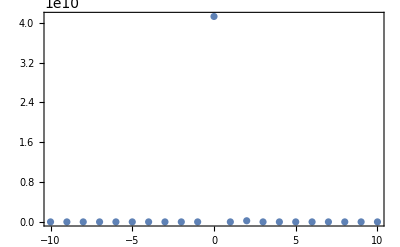
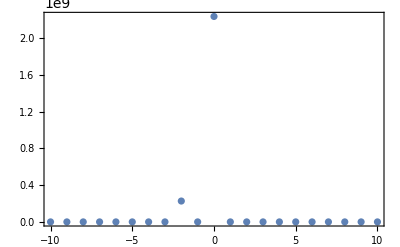

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*^^^^^^-примеры-^^^^^^*)
```

```mathematica
(*vvvvvvv+старое+vvvvvvvv*)
```

```mathematica
2^(Floor[Log[2,20 mMax]])
```

128

```mathematica
llts1=AmplTwistTab[1,1.5/mee,1.5/mee/γ];
lltsm1=AmplTwistTab[-1,1.5/mee,1.5/mee/γ];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

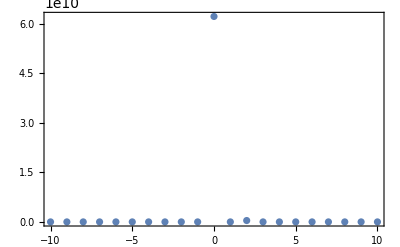
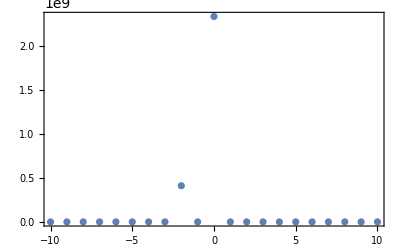

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*новое около вкб*)
```

```mathematica
dProbabPlane[1,90/mee,0.02,0.000000001]//Timing
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.97059×10^7}. NIntegrate obtained -275208.+7373.61 ⅈ and 3403.05 for the integral and error estimates.

{1.18561,20663.1}

```mathematica
tplp1=Module[{xx},ParallelTable[{xx,dProbabPlane[1,xx/mee,0.02,0.000000001]},{xx,85,95,0.1}]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.00282×10^7}. NIntegrate obtained 5742.01+4532.43 ⅈ and 4166.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.85663×10^7}. NIntegrate obtained 23631.8-62564.6 ⅈ and 5746. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained 10113.6-14136.2 ⅈ and 3297.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained -22208.9-16288.7 ⅈ and 2941.54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.85663×10^7}. NIntegrate obtained -62951.2-25187.2 ⅈ and 5618.34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.85663×10^7}. NIntegrate obtained -26032.3+62749.5 ⅈ and 6014.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.45184×10^7}. NIntegrate obtained 92806.1-76285.4 ⅈ and 1631.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.45184×10^7}. NIntegrate obtained -75463.9-95516.4 ⅈ and 2041.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.44435×10^7}. NIntegrate obtained -96602.9+73150.5 ⅈ and 2387.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34766×10^7}. NIntegrate obtained -4593.94-7981.95 ⅈ and 5037.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.93836×10^7}. NIntegrate obtained 11956.8-840.837 ⅈ and 5133.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55831×10^7}. NIntegrate obtained -6594.68-33628.5 ⅈ and 5152.56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.00282×10^7}. NIntegrate obtained 329499.+11012.2 ⅈ and 1955.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.85663×10^7}. NIntegrate obtained 23687.8-356742. ⅈ and 1738.05 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -381338.-37580.7 ⅈ and 1532.26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.149×10^7}. NIntegrate obtained 251119.-525544. ⅈ and 2158.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.59351×10^7}. NIntegrate obtained -521922.-271208. ⅈ and 2010.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55831×10^7}. NIntegrate obtained 393636.-334475. ⅈ and 1451.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34766×10^7}. NIntegrate obtained -290965.+515185. ⅈ and 2036.54 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.7397×10^7}. NIntegrate obtained -309407.-389515. ⅈ and 1321.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.7397×10^7}. NIntegrate obtained -383711.+283644. ⅈ and 1216.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97509×10^7}. NIntegrate obtained 216941.-54325.6 ⅈ and 531.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97509×10^7}. NIntegrate obtained -40293.3-193211. ⅈ and 621.043 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.42411×10^7}. NIntegrate obtained -168890.+28411.4 ⅈ and 731.024 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tplm1=Module[{xx},ParallelTable[{xx,dProbabPlane[-1,xx/mee,0.02,0.000000001]},{xx,85,95,0.1}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.50881×10^7}. NIntegrate obtained -1411.63+86.214 ⅈ and 3051.58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained -11798.4+39893.5 ⅈ and 5769.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.55754×10^7}. NIntegrate obtained 38914.9+11408. ⅈ and 5883.14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.50881×10^7}. NIntegrate obtained -4832.41+6812.06 ⅈ and 2730.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.58977×10^7}. NIntegrate obtained 12016.5-36538.2 ⅈ and 5466.01 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.50881×10^7}. NIntegrate obtained 13145.5+9744.89 ⅈ and 2396.92 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61758×10^6}. NIntegrate obtained -49753.5+37404.9 ⅈ and 2398.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.99831×10^7}. NIntegrate obtained 36609.5+52866.9 ⅈ and 2673.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.15649×10^7}. NIntegrate obtained 55733.6-34914.1 ⅈ and 2954.72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.50056×10^7}. NIntegrate obtained -3191.16+1734.47 ⅈ and 4988.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.50056×10^7}. NIntegrate obtained -8081.46+8269.59 ⅈ and 5101.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.50056×10^7}. NIntegrate obtained 11877.1+18344.9 ⅈ and 5142.77 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained -173399.-8126.46 ⅈ and 1842.11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained -13468.6+186801. ⅈ and 1723.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51783×10^7}. NIntegrate obtained 200241.+19469.5 ⅈ and 1647.82 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.80416×10^7}. NIntegrate obtained -133801.+259324. ⅈ and 2625.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.80416×10^7}. NIntegrate obtained 258358.+144271. ⅈ and 2895.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.57327×10^7}. NIntegrate obtained 153126.-255869. ⅈ and 2850.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.57854×10^7}. NIntegrate obtained -189841.+157771. ⅈ and 1338.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.75994×10^7}. NIntegrate obtained 144119.+188823. ⅈ and 1190.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.75994×10^7}. NIntegrate obtained 186880.-131145. ⅈ and 1042.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.03955×10^7}. NIntegrate obtained -100181.+32764.9 ⅈ and 672.621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97509×10^7}. NIntegrate obtained 25616.4+87380.6 ⅈ and 740.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97509×10^7}. NIntegrate obtained 74769.1-19057.4 ⅈ and 806.591 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

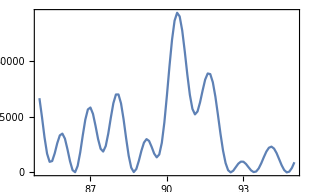
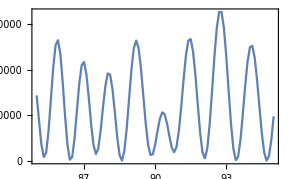

```mathematica
{ListLinePlot[tplp1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tplm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llts1=AmplTwistTab[1,90.4/mee,90.4/mee 0.02];
lltsm1=AmplTwistTab[-1,90.4/mee,90.4/mee 0.02];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -381338.-37580.7 ⅈ and 1532.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained -28349.4+392330. ⅈ and 1529.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -383247.+962.162 ⅈ and 1533.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained 10220.7+394285. ⅈ and 1533.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -381336.+39537.8 ⅈ and 1572.42 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained 48744.4+392416. ⅈ and 1570.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.73221×10^7}. NIntegrate obtained 401322.+39414.8 ⅈ and 1529.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.35514×10^7}. NIntegrate obtained 403463.+983.955 ⅈ and 1529.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.35514×10^7}. NIntegrate obtained 401606.-37603.1 ⅈ and 1566.13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained 48690.2-390423. ⅈ and 1532.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained 10148.6-392338. ⅈ and 1536.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained -28470.1-390536. ⅈ and 1576.73 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -381338.-37580.7 ⅈ and 1532.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -383247.+962.162 ⅈ and 1533.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.26074×10^6}. NIntegrate obtained -381336.+39537.8 ⅈ and 1572.42 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained -28349.4+392330. ⅈ and 1529.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained 10220.7+394285. ⅈ and 1533.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.44061×10^7}. NIntegrate obtained 48744.4+392416. ⅈ and 1570.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.73221×10^7}. NIntegrate obtained 401322.+39414.8 ⅈ and 1529.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained 48690.2-390423. ⅈ and 1532.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.35514×10^7}. NIntegrate obtained 403463.+983.955 ⅈ and 1529.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.35514×10^7}. NIntegrate obtained 401606.-37603.1 ⅈ and 1566.13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained 10148.6-392338. ⅈ and 1536.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.02237×10^6}. NIntegrate obtained -28470.1-390536. ⅈ and 1576.73 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51783×10^7}. NIntegrate obtained 200241.+19469.5 ⅈ and 1647.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.30267×10^7}. NIntegrate obtained 203703.+16916.6 ⅈ and 1646.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained 200320.+19024. ⅈ and 1647.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.30267×10^7}. NIntegrate obtained 204027.+16991.8 ⅈ and 1643.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained 200448.+18795.9 ⅈ and 1644.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.78018×10^7}. NIntegrate obtained 204323.+17000.8 ⅈ and 1657.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206369.+20075.3 ⅈ and 1640.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206329.+20350.9 ⅈ and 1643.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206240.+20684.3 ⅈ and 1661.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.08003×10^7}. NIntegrate obtained 202876.+22707.2 ⅈ and 1635.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.54104×10^7}. NIntegrate obtained 202689.+22656.1 ⅈ and 1639.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.54104×10^7}. NIntegrate obtained 202448.+22545.8 ⅈ and 1635.76 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51783×10^7}. NIntegrate obtained 200241.+19469.5 ⅈ and 1647.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained 200320.+19024. ⅈ and 1647.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.03424×10^8}. NIntegrate obtained 200448.+18795.9 ⅈ and 1644.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.30267×10^7}. NIntegrate obtained 203703.+16916.6 ⅈ and 1646.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.30267×10^7}. NIntegrate obtained 204027.+16991.8 ⅈ and 1643.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.78018×10^7}. NIntegrate obtained 204323.+17000.8 ⅈ and 1657.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206369.+20075.3 ⅈ and 1640.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206329.+20350.9 ⅈ and 1643.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.08003×10^7}. NIntegrate obtained 202876.+22707.2 ⅈ and 1635.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74046×10^7}. NIntegrate obtained 206240.+20684.3 ⅈ and 1661.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.54104×10^7}. NIntegrate obtained 202689.+22656.1 ⅈ and 1639.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.54104×10^7}. NIntegrate obtained 202448.+22545.8 ⅈ and 1635.76 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

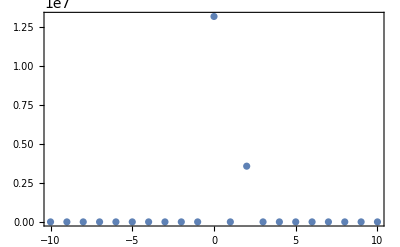
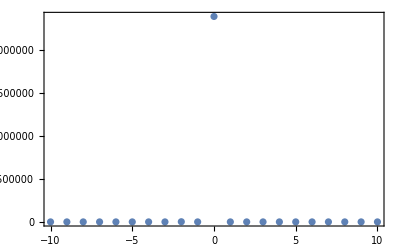

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llts2=AmplTwistTab[1,91.8/mee,91.8/mee 0.02];
lltsm2=AmplTwistTab[-1,91.8/mee,91.8/mee 0.02];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained 310098.-506798. ⅈ and 2132.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained 506138.+309422. ⅈ and 2061.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained 258997.-534748. ⅈ and 2136.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.29442×10^7}. NIntegrate obtained 205399.-557557. ⅈ and 2119.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained 534100.+258321. ⅈ and 2058.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.08454×10^7}. NIntegrate obtained 556921.+204697. ⅈ and 2055.92 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.50133×10^7}. NIntegrate obtained -505959.-310749. ⅈ and 2097.54 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.50133×10^7}. NIntegrate obtained -533946.-259672. ⅈ and 2047.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.61826×10^7}. NIntegrate obtained -556762.-206060. ⅈ and 2045.56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31917×10^7}. NIntegrate obtained -310040.+505368. ⅈ and 2071.29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.71121×10^7}. NIntegrate obtained -258948.+533393. ⅈ and 2158.17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.73145×10^7}. NIntegrate obtained -205357.+556214. ⅈ and 2159.13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained 506138.+309422. ⅈ and 2061.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.03505×10^7}. NIntegrate obtained 534100.+258321. ⅈ and 2058.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.08454×10^7}. NIntegrate obtained 556921.+204697. ⅈ and 2055.92 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained 310098.-506798. ⅈ and 2132.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained 258997.-534748. ⅈ and 2136.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.29442×10^7}. NIntegrate obtained 205399.-557557. ⅈ and 2119.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.50133×10^7}. NIntegrate obtained -505959.-310749. ⅈ and 2097.54 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.50133×10^7}. NIntegrate obtained -533946.-259672. ⅈ and 2047.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.61826×10^7}. NIntegrate obtained -556762.-206060. ⅈ and 2045.56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31917×10^7}. NIntegrate obtained -310040.+505368. ⅈ and 2071.29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.71121×10^7}. NIntegrate obtained -258948.+533393. ⅈ and 2158.17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.73145×10^7}. NIntegrate obtained -205357.+556214. ⅈ and 2159.13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.57327×10^7}. NIntegrate obtained -251948.-161194. ⅈ and 2818.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.19773×10^7}. NIntegrate obtained -250287.-160058. ⅈ and 2847.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.10478×10^7}. NIntegrate obtained -251783.-161282. ⅈ and 2785.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained -250285.-159933. ⅈ and 2855.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.10478×10^7}. NIntegrate obtained -251629.-161276. ⅈ and 2796.99 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.54555×10^7}. NIntegrate obtained -250343.-159801. ⅈ and 2852.89 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.27044×10^7}. NIntegrate obtained -251930.-158519. ⅈ and 2864.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.6385×10^7}. NIntegrate obtained -251966.-158506. ⅈ and 2851.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.73145×10^7}. NIntegrate obtained -253444.-159704. ⅈ and 2870.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.38737×10^7}. NIntegrate obtained -252088.-158488. ⅈ and 2848.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.48032×10^7}. NIntegrate obtained -253420.-159845. ⅈ and 2896.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.48032×10^7}. NIntegrate obtained -253357.-159982. ⅈ and 2910.19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.57327×10^7}. NIntegrate obtained -251948.-161194. ⅈ and 2818.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.10478×10^7}. NIntegrate obtained -251783.-161282. ⅈ and 2785.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.10478×10^7}. NIntegrate obtained -251629.-161276. ⅈ and 2796.99 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.19773×10^7}. NIntegrate obtained -250287.-160058. ⅈ and 2847.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.17749×10^7}. NIntegrate obtained -250285.-159933. ⅈ and 2855.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.54555×10^7}. NIntegrate obtained -250343.-159801. ⅈ and 2852.89 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.27044×10^7}. NIntegrate obtained -251930.-158519. ⅈ and 2864.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.6385×10^7}. NIntegrate obtained -251966.-158506. ⅈ and 2851.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.38737×10^7}. NIntegrate obtained -252088.-158488. ⅈ and 2848.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.73145×10^7}. NIntegrate obtained -253444.-159704. ⅈ and 2870.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.48032×10^7}. NIntegrate obtained -253420.-159845. ⅈ and 2896.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.48032×10^7}. NIntegrate obtained -253357.-159982. ⅈ and 2910.19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tms2=Table[{m,dProbabTwist[m,llts2[[3]]]},{m,-mMax,mMax}];
tmsm2=Table[{m,dProbabTwist[m,lltsm2[[3]]]},{m,-mMax,mMax}];
```

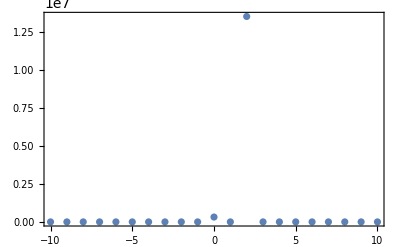
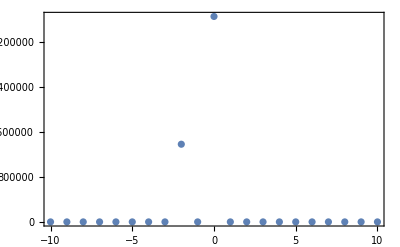

```mathematica
{ListPlot[tms2,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm2,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*спектр*)
```

```mathematica
2(ϵpp[25/mee]^(-1/2)-1)
2(ϵpl[25/mee]^(-1/2)-1)
```

0.288704

1.7083

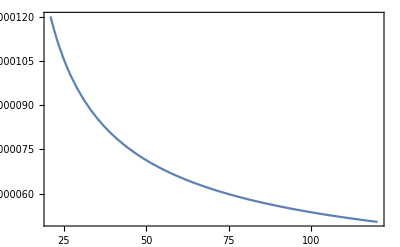
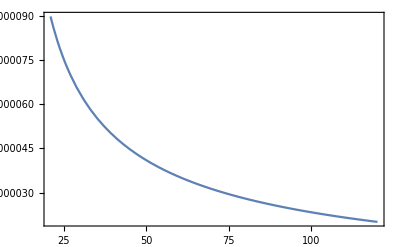
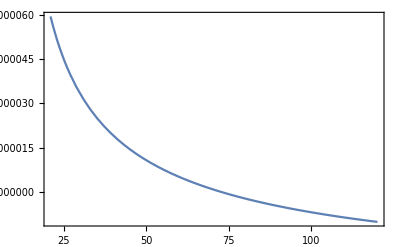
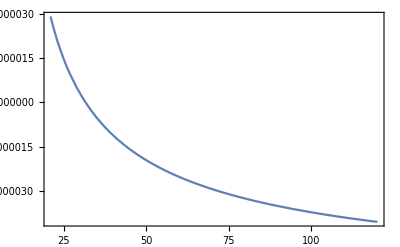

```mathematica
{Plot[EqnSpecX[xx/mee,1/100,-2],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,-1],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,0],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,1],{xx,ωp mee,120},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/100,0],{xx,80}]
FindRoot[EqnSpecX[xx/mee,1/100,1],{xx,30}]
```

{xx→72.5465}

{xx→31.636}

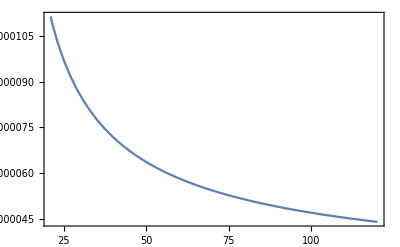
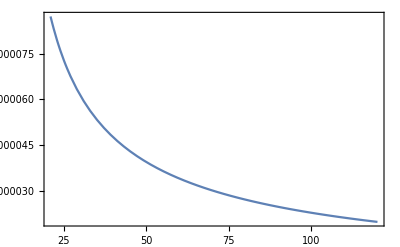
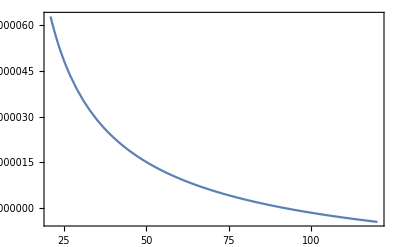
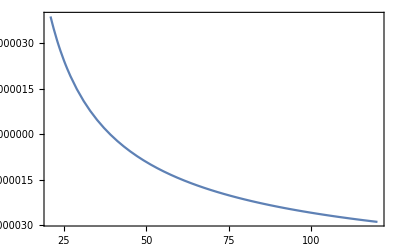

```mathematica
{Plot[EqnSpecX[xx/mee,0.02,-2],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,0.02,-1],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,0.02,0],{xx,ωp mee,120},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,0.02,1],{xx,ωp mee,120},Frame->True,PlotRange->Full]}
```

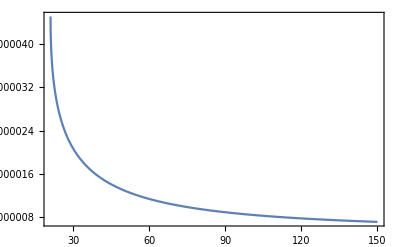
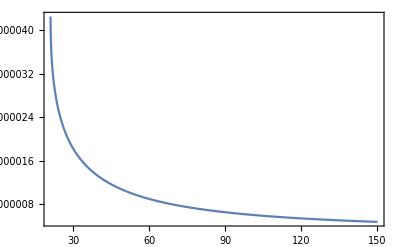
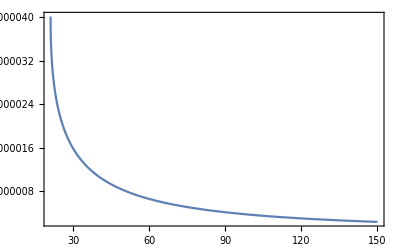
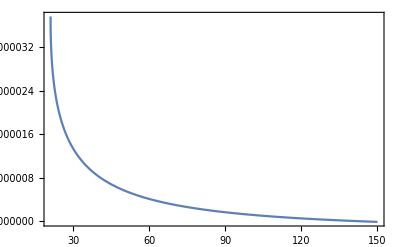

```mathematica
{Plot[EqnSpecY[xx/mee,0.02,-2],{xx,ωp mee,150},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,0.02,-1],{xx,ωp mee,150},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,0.02,0],{xx,ωp mee,150},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,0.02,1],{xx,ωp mee,150},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,0.02,0],{xx,45}]
FindRoot[EqnSpecX[xx/mee,0.02,1],{xx,80}]
```

{xx→91.7911}

{xx→39.0493}

```mathematica
FindRoot[EqnSpecY[xx/mee,0.02,1],{xx,80}]
```

{xx→144.922}

```mathematica
FindRoot[EqnSpecY[xx/mee,0.02,0],{xx,80}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{xx→868.942}

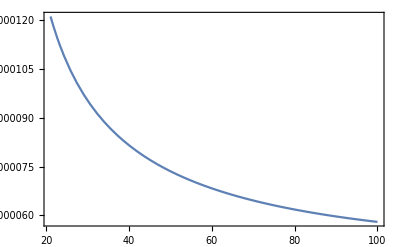
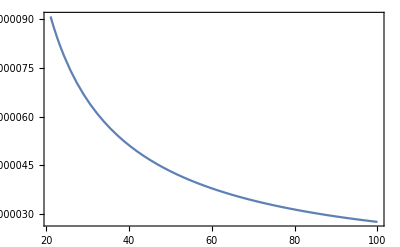
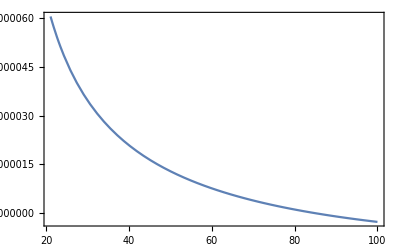
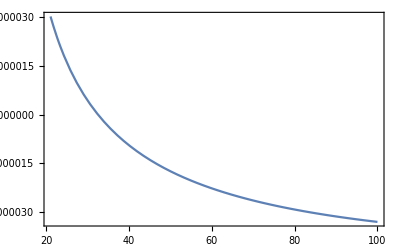

```mathematica
{Plot[EqnSpecX[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/15,0],{xx,80}]
FindRoot[EqnSpecX[xx/mee,1/15,1],{xx,30}]
```

{xx→85.0019}

{xx→32.5328}

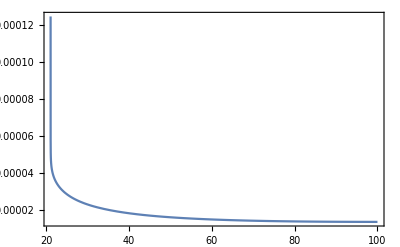
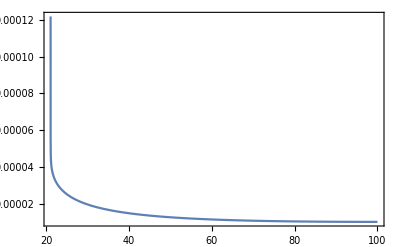
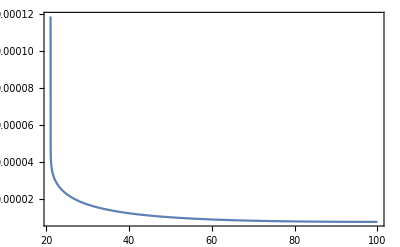
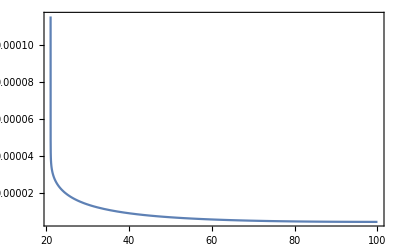

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
EqnSpecY[xx/mee,1/5,1]/.{xx->80}
```

4.68235×10^-6

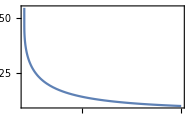
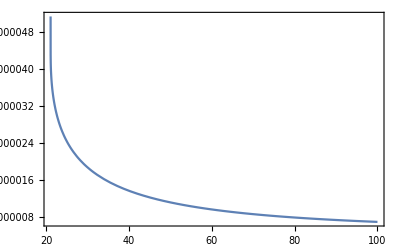
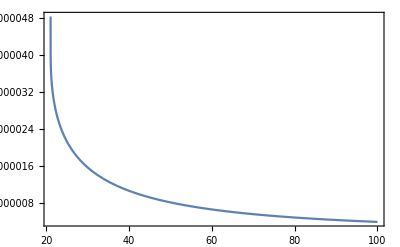
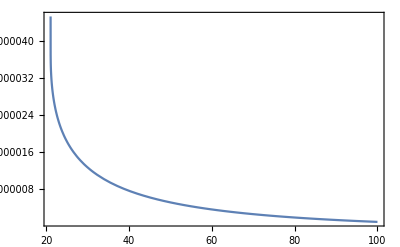

```mathematica
{Plot[EqnSpecY[xx/mee,1/15,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/15,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

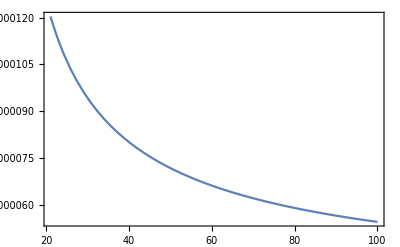
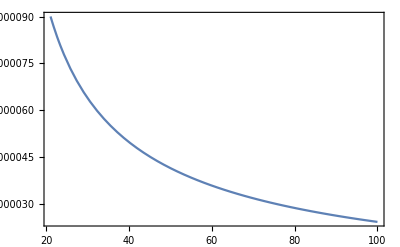
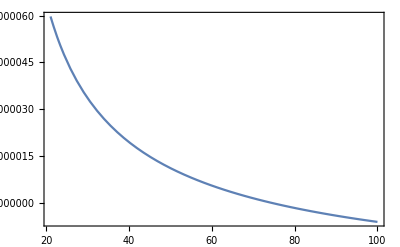
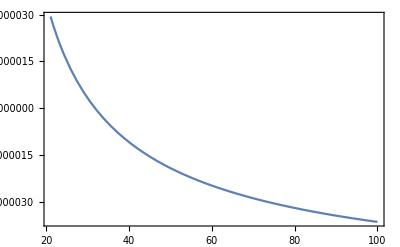

```mathematica
{Plot[EqnSpecX[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/30,0],{xx,40}]
FindRoot[EqnSpecX[xx/mee,1/30,1],{xx,40}]
```

{xx→74.8289}

{xx→31.8363}

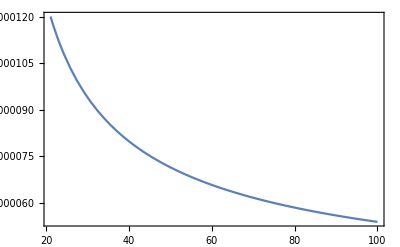
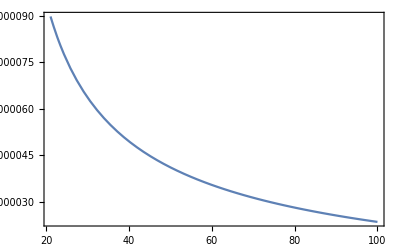
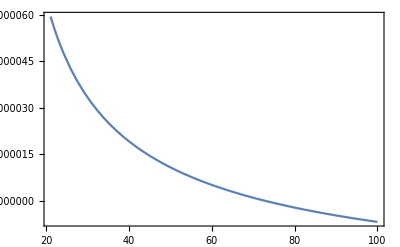
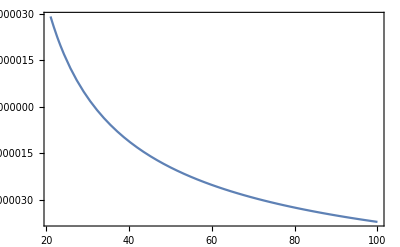

```mathematica
{Plot[EqnSpecX[xx/mee,1/60,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/60,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/60,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/60,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/60,0],{xx,40}]
```

{xx→72.9289}

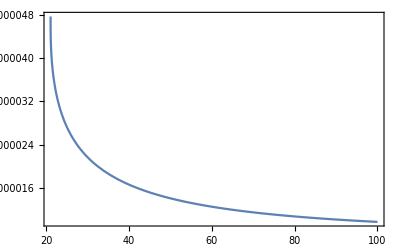
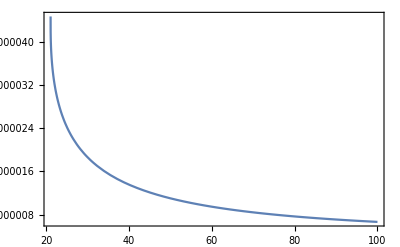
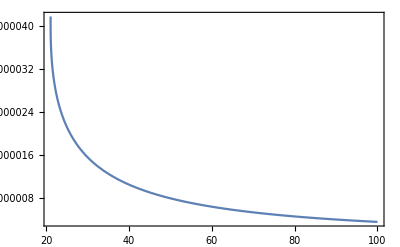
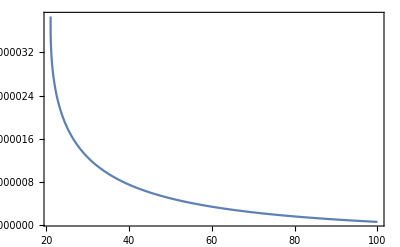

```mathematica
{Plot[EqnSpecY[xx/mee,1/30,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/30,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
EqnSpecY[xx/mee,1/30,1]/.{xx->100}
```

5.91963×10^-7

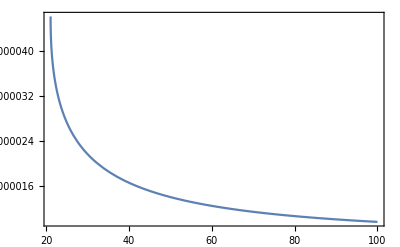
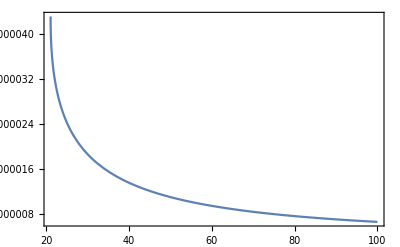
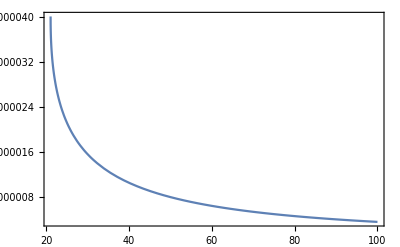
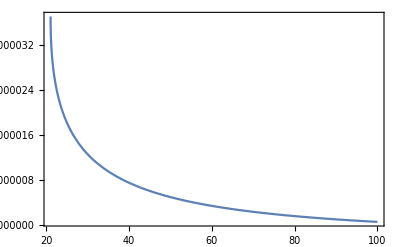

```mathematica
{Plot[EqnSpecY[xx/mee,1/60,-2],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/60,-1],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/60,0],{xx,ωp mee,100},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/60,1],{xx,ωp mee,100},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/60,1],{xx,60}]
```

{xx→114.87}

```mathematica
dProbabPlane[1,30/mee,1/15,0]//Timing
dProbabPlane[1,31/mee,1/15,0]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.57714×10^6}. NIntegrate obtained -783.31+389.643 ⅈ and 858.759 for the integral and error estimates.

{4.27443,5444.83}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.67158×10^7}. NIntegrate obtained -4660.01-431.307 ⅈ and 1149.39 for the integral and error estimates.

{4.22763,4072.78}

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/15,0]},{x,26,34,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.9227×10^7}. NIntegrate obtained 3455.14+1110.03 ⅈ and 215.893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.40208×10^7}. NIntegrate obtained -2700.85+606.709 ⅈ and 298.254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained -1012.13+699.297 ⅈ and 219.964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.54002×10^7}. NIntegrate obtained 1351.2-1611.2 ⅈ and 303.972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.78477×10^7}. NIntegrate obtained -517.004+4054.22 ⅈ and 224.265 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20419×10^7}. NIntegrate obtained 822.907-4404.77 ⅈ and 309.516 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1086×10^7}. NIntegrate obtained 2998.46+2692.42 ⅈ and 398.631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.35973×10^7}. NIntegrate obtained 876.432-61.1591 ⅈ and 405.643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.94481×10^7}. NIntegrate obtained -2999.98+396.519 ⅈ and 412.886 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21431×10^7}. NIntegrate obtained -1285.07-3682.02 ⅈ and 524.241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.86874×10^6}. NIntegrate obtained 76.5249-96.6595 ⅈ and 533.607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.31738×10^7}. NIntegrate obtained 2942.67+2424.86 ⅈ and 542.659 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.14721×10^7}. NIntegrate obtained -1873.13-2787.74 ⅈ and 681.181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.90246×10^7}. NIntegrate obtained -3167.65-3650.41 ⅈ and 691.871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.94856×10^7}. NIntegrate obtained -2364.08-2055.3 ⅈ and 702.68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.50141×10^7}. NIntegrate obtained -3605.61+1793.18 ⅈ and 871.962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.67158×10^7}. NIntegrate obtained -4416.43+2298.89 ⅈ and 884.907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.96994×10^6}. NIntegrate obtained -2848.33+1501.07 ⅈ and 898.679 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.27503×10^7}. NIntegrate obtained 279.607+107.938 ⅈ and 1101.69 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {302792.}. NIntegrate obtained -237.739+4786.19 ⅈ and 1374.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.09512×10^6}. NIntegrate obtained -3098.06+281.312 ⅈ and 1117.76 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.53364×10^7}. NIntegrate obtained -1198.27+5268.01 ⅈ and 1394.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.34961×10^7}. NIntegrate obtained -5011.25-48.5464 ⅈ and 1133.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.06251×10^7}. NIntegrate obtained -1524.+3809.31 ⅈ and 1413.05 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.71393×10^7}. NIntegrate obtained -358.193+5720.83 ⅈ and 1699.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.75441×10^7}. NIntegrate obtained -2715.63+1775.79 ⅈ and 2076.51 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.30726×10^7}. NIntegrate obtained -1752.32+5085.08 ⅈ and 1720.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.92457×10^7}. NIntegrate obtained -5808.74+2605.13 ⅈ and 2087.85 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.04716×10^6}. NIntegrate obtained -5501.27-93.1978 ⅈ and 2130.18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.96692×10^7}. NIntegrate obtained -1836.19+2899.31 ⅈ and 1742.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 3494.19
26.05 | 3263.81
26.1 | 1507.59
26.15 | 5150.9
26.2 | 464.768
26.25 | 6103.34
26.3 | 110.886
26.35 | 5555.82
26.4 | 120.749
26.45 | 4709.87
26.5 | 585.262
26.55 | 4512.61
26.6 | 928.678
26.65 | 5121.7
26.7 | 1059.74
26.75 | 5366.22
26.8 | 725.339
26.85 | 4851.63
26.9 | 449.066
26.95 | 4386.69
27. | 286.136
27.05 | 5164.02
27.1 | 42.9761
27.15 | 6121.88
27.2 | 336.969
27.25 | 5410.64
27.3 | 1363.44
27.35 | 3491.06
27.4 | 2393.37
27.45 | 1950.3
27.5 | 3544.35
27.55 | 771.4
27.6 | 5346.98
27.65 | 35.7574
27.7 | 5522.92
27.75 | 1549.32
27.8 | 2621.97
27.85 | 3924.2
27.9 | 269.435
27.95 | 4557.76
28. | 207.492
28.05 | 3838.89
28.1 | 2184.63
28.15 | 1460.5
28.2 | 5503.12
28.25 | 192.88
28.3 | 4680.38
28.35 | 3120.35
28.4 | 687.792
28.45 | 4800.22
28.5 | 432.877
28.55 | 2944.31
28.6 | 3012.74
28.65 | 292.814
28.7 | 5193.58
28.75 | 1524.41
28.8 | 1886.8
28.85 | 5625.12
28.9 | 534.741
28.95 | 2929.75
29. | 4091.06
29.05 | 7.38336
29.1 | 3478.63
29.15 | 2328.75
29.2 | 358.546
29.25 | 4607.26
29.3 | 1691.87
29.35 | 1053.16
29.4 | 5630.04
29.45 | 1768.12
29.5 | 1135.68
29.55 | 5233.28
29.6 | 1557.39
29.65 | 953.964
29.7 | 4273.24
29.75 | 1085.47
29.8 | 1198.62
29.85 | 4543.49
29.9 | 1244.6
29.95 | 1189.99
30. | 5444.83
30.05 | 2279.38
30.1 | 471.244
30.15 | 4788.44
30.2 | 3157.29
30.25 | 22.7666
30.3 | 3175.63
30.35 | 3253.9
30.4 | 27.6106
30.45 | 2609.13
30.5 | 4002.14
30.55 | 470.717
30.6 | 1819.52
30.65 | 5325.8
30.7 | 2202.93
30.75 | 322.726
30.8 | 4244.67
30.85 | 4116.91
30.9 | 239.539
30.95 | 1780.99
31. | 4072.78
31.05 | 1258.96
31.1 | 437.053
31.15 | 3719.63
31.2 | 2913.08
31.25 | 56.7995
31.3 | 2445.04
31.35 | 5197.65
31.4 | 2144.81
31.45 | 278.691
31.5 | 3708.54
31.55 | 4603.32
31.6 | 1032.03
31.65 | 524.437
31.7 | 3467.15
31.75 | 2749.49
31.8 | 87.0859
31.85 | 1634.47
31.9 | 4120.12
31.95 | 2170.04
32. | 64.3797
32.05 | 2804.48
32.1 | 5166.53
32.15 | 2410.43
32.2 | 122.718
32.25 | 2665.03
32.3 | 4739.
32.35 | 2251.13
32.4 | 10.5361
32.45 | 1936.18
32.5 | 3587.15
32.55 | 1478.58
32.6 | 46.0543
32.65 | 2424.12
32.7 | 4198.19
32.75 | 2005.34
32.8 | 76.0611
32.85 | 2353.26
32.9 | 5044.77
32.95 | 3438.35
33. | 394.772
33.05 | 1102.73
33.1 | 3885.57
33.15 | 3586.31
33.2 | 776.012
33.25 | 279.474
33.3 | 2578.23
33.35 | 3329.57
33.4 | 1155.06
33.45 | 71.9417
33.5 | 2311.31
33.55 | 4367.42
33.6 | 2890.05
33.65 | 358.111
33.7 | 1076.47
33.75 | 4072.68
33.8 | 4676.65
33.85 | 1966.76
33.9 | 75.1481
33.95 | 1560.18
34. | 3643.18)

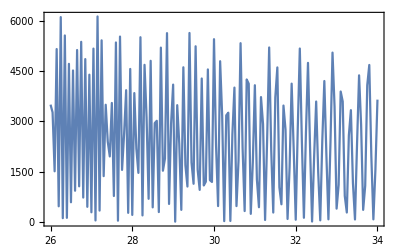

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/15,0]},{x,26,34,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.53815×10^7}. NIntegrate obtained 3231.54+2165.96 ⅈ and 336.202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.66333×10^7}. NIntegrate obtained -4260.52+4945.19 ⅈ and 447.124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.86573×10^7}. NIntegrate obtained -5041.36+160.02 ⅈ and 341.975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.69556×10^7}. NIntegrate obtained 23.0729-1139.96 ⅈ and 454.377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.45081×10^7}. NIntegrate obtained -3562.33-284.439 ⅈ and 347.755 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.77277×10^7}. NIntegrate obtained 1685.61-5055.28 ⅈ and 462.03 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.39009×10^7}. NIntegrate obtained -3002.53-1409.48 ⅈ and 578.046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97517×10^7}. NIntegrate obtained 742.727-8929.67 ⅈ and 587.179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.31551×10^7}. NIntegrate obtained -6144.1-3457. ⅈ and 739.367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.07824×10^7}. NIntegrate obtained 2938.62-5065.87 ⅈ and 596.308 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.46093×10^7}. NIntegrate obtained -1682.86-1555.68 ⅈ and 749.98 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.21618×10^7}. NIntegrate obtained 3690.46+3334.6 ⅈ and 761.281 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.69033×10^6}. NIntegrate obtained 1551.43-7736.46 ⅈ and 934.022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.12059×10^7}. NIntegrate obtained 3537.05-3600.53 ⅈ and 947.381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.08836×10^7}. NIntegrate obtained -245.61-7219.28 ⅈ and 1169.13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.12059×10^7}. NIntegrate obtained 1151.5+5424.72 ⅈ and 960.93 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.05613×10^7}. NIntegrate obtained 4561.1+1224.15 ⅈ and 1183.55 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.39647×10^7}. NIntegrate obtained 3062.89+8924.57 ⅈ and 1196.32 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51791×10^7}. NIntegrate obtained 3639.24-8691.5 ⅈ and 1445.53 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.2263×10^7}. NIntegrate obtained 3585.14-1431.23 ⅈ and 1463.44 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained 2731.4+508.767 ⅈ and 1771.86 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.82712×10^7}. NIntegrate obtained -2286.47+3932.29 ⅈ and 1483.72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.93282×10^7}. NIntegrate obtained 2621.53+6531.74 ⅈ and 1794.22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.2263×10^7}. NIntegrate obtained -948.038+6327.75 ⅈ and 1816.86 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 3601.02+3737.45 ⅈ and 2151.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 759.404+7525.13 ⅈ and 2177.08 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained -289.515+1533.88 ⅈ and 2588.98 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained -2217.35+4476.62 ⅈ and 2203.94 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained -5705.6+2608.64 ⅈ and 2618.2 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {505190.}. NIntegrate obtained -7103.76-1397.07 ⅈ and 2647.43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 5131.17
26.05 | 3662.83
26.1 | 2469.87
26.15 | 5004.11
26.2 | 600.099
26.25 | 6289.24
26.3 | 43.0979
26.35 | 6872.16
26.4 | 330.892
26.45 | 7105.49
26.5 | 534.53
26.55 | 6240.81
26.6 | 640.533
26.65 | 5308.49
26.7 | 1094.25
26.75 | 5243.05
26.8 | 1356.47
26.85 | 6051.07
26.9 | 876.913
26.95 | 6924.52
27. | 196.685
27.05 | 6702.78
27.1 | 73.8319
27.15 | 6090.06
27.2 | 299.073
27.25 | 5840.96
27.3 | 997.887
27.35 | 5143.08
27.4 | 3086.42
27.45 | 2924.64
27.5 | 5712.05
27.55 | 560.928
27.6 | 6429.6
27.65 | 160.838
27.7 | 5343.55
27.75 | 1327.39
27.8 | 3464.65
27.85 | 4194.21
27.9 | 794.548
27.95 | 7082.72
28. | 385.372
28.05 | 5210.61
28.1 | 3557.96
28.15 | 1090.48
28.2 | 5782.62
28.25 | 233.441
28.3 | 4902.58
28.35 | 2787.93
28.4 | 1450.49
28.45 | 6572.34
28.5 | 435.223
28.55 | 4666.68
28.6 | 4939.81
28.65 | 127.566
28.7 | 5954.08
28.75 | 2123.92
28.8 | 1622.48
28.85 | 5455.29
28.9 | 344.238
28.95 | 4079.46
29. | 4732.51
29.05 | 37.8691
29.1 | 5887.12
29.15 | 3977.96
29.2 | 281.477
29.25 | 5993.11
29.3 | 2773.79
29.35 | 737.787
29.4 | 5523.22
29.45 | 1615.3
29.5 | 1518.47
29.55 | 5923.62
29.6 | 1290.76
29.65 | 1973.48
29.7 | 6653.8
29.75 | 1805.66
29.8 | 1486.04
29.85 | 6382.77
29.9 | 2277.62
29.95 | 796.527
30. | 5449.27
30.05 | 2304.66
30.1 | 603.205
30.15 | 5330.17
30.2 | 2980.31
30.25 | 241.355
30.3 | 5287.17
30.35 | 5017.26
30.4 | 62.6486
30.45 | 3656.
30.5 | 6078.82
30.55 | 1138.29
30.6 | 1404.8
30.65 | 5442.32
30.7 | 2301.46
30.75 | 389.86
30.8 | 4680.12
30.85 | 4073.54
30.9 | 59.5133
30.95 | 3289.36
31. | 6310.11
31.05 | 1952.21
31.1 | 587.752
31.15 | 5471.98
31.2 | 4809.36
31.25 | 325.005
31.3 | 2060.77
31.35 | 5321.01
31.4 | 2189.72
31.45 | 294.588
31.5 | 4191.63
31.55 | 4787.98
31.6 | 688.181
31.65 | 1379.99
31.7 | 5970.96
31.75 | 4527.64
31.8 | 205.952
31.85 | 2165.73
31.9 | 5984.41
31.95 | 3667.32
32. | 89.7264
32.05 | 2390.57
32.1 | 5128.7
32.15 | 2312.07
32.2 | 135.648
32.25 | 3290.96
32.3 | 5374.34
32.35 | 2091.92
32.4 | 111.448
32.45 | 3826.43
32.5 | 6294.82
32.55 | 2774.07
32.6 | 6.5327
32.65 | 2979.6
32.7 | 5767.05
32.75 | 3189.17
32.8 | 118.123
32.85 | 1965.72
32.9 | 4862.51
32.95 | 3171.7
33. | 181.457
33.05 | 1739.84
33.1 | 5226.96
33.15 | 4351.28
33.2 | 664.678
33.25 | 791.183
33.3 | 4724.82
33.35 | 5931.49
33.4 | 2438.55
33.45 | 7.17135
33.5 | 2360.86
33.55 | 5261.3
33.6 | 3803.25
33.65 | 524.709
33.7 | 850.261
33.75 | 3972.62
33.8 | 4487.12
33.85 | 1515.63
33.9 | 117.528
33.95 | 2869.31
34. | 5680.79)

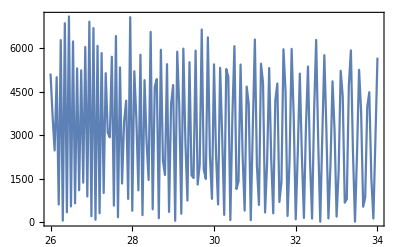

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk06s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,26,34,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.40208×10^7}. NIntegrate obtained -649.449-773.636 ⅈ and 150.432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.1251×10^7}. NIntegrate obtained 306.84+1713.46 ⅈ and 108.708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.35973×10^7}. NIntegrate obtained 1297.86+349.038 ⅈ and 153.294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.57225×10^7}. NIntegrate obtained 1877.77-843.762 ⅈ and 156.119 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.09287×10^7}. NIntegrate obtained -917.618-467.273 ⅈ and 110.897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.78477×10^7}. NIntegrate obtained -1799.86+785.272 ⅈ and 113.059 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1086×10^7}. NIntegrate obtained -190.919+2099.21 ⅈ and 201.085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.35973×10^7}. NIntegrate obtained -7.01699+135.54 ⅈ and 204.682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.15095×10^7}. NIntegrate obtained -1324.92-1348.46 ⅈ and 208.372 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21431×10^7}. NIntegrate obtained 878.798-1587.32 ⅈ and 264.418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {403991.}. NIntegrate obtained 44.3791+226.113 ⅈ and 269.237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.55315×10^6}. NIntegrate obtained 162.615+2081.76 ⅈ and 273.785 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.14721×10^7}. NIntegrate obtained 191.249-1818.19 ⅈ and 343.704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.90246×10^7}. NIntegrate obtained -19.046-2503.66 ⅈ and 349.041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.94856×10^7}. NIntegrate obtained -140.572-1525.22 ⅈ and 354.605 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.08649×10^7}. NIntegrate obtained -2186.86-360.152 ⅈ and 439.986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.25666×10^7}. NIntegrate obtained -2529.07-446.498 ⅈ and 446.572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.82078×10^6}. NIntegrate obtained -1447.96-336.681 ⅈ and 453.79 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -188.548+168.72 ⅈ and 556.024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.09512×10^6}. NIntegrate obtained -1714.54-746.641 ⅈ and 564.05 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.34961×10^7}. NIntegrate obtained -2290.56-1439.87 ⅈ and 572.201 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.07114×10^6}. NIntegrate obtained -1229.99+2361.98 ⅈ and 693.984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.96994×10^6}. NIntegrate obtained -1778.44+2145.57 ⅈ and 703.673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.09512×10^6}. NIntegrate obtained -1447.2+1218.58 ⅈ and 713.141 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.71393×10^7}. NIntegrate obtained -814.682+2646.14 ⅈ and 857.639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.30726×10^7}. NIntegrate obtained -1343.59+2310.64 ⅈ and 868.303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.96692×10^7}. NIntegrate obtained -1227.58+1364.93 ⅈ and 879.073 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.75441×10^7}. NIntegrate obtained -1778.29+667.129 ⅈ and 1047.89 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.92457×10^7}. NIntegrate obtained -2636.18+146.381 ⅈ and 1061.75 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.04716×10^6}. NIntegrate obtained -2689.72-574.574 ⅈ and 1075. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(26. | 20764.9
26.05 | 2170.68
26.1 | 15313.7
26.15 | 10089.8
26.2 | 8214.98
26.25 | 17052.2
26.3 | 5502.09
26.35 | 21189.4
26.4 | 2868.77
26.45 | 20103.3
26.5 | 397.351
26.55 | 19055.9
26.6 | 40.3417
26.65 | 21609.6
26.7 | 86.3489
26.75 | 24328.4
26.8 | 438.485
26.85 | 23335.5
26.9 | 520.22
26.95 | 19278.8
27. | 938.998
27.05 | 17090.7
27.1 | 2013.92
27.15 | 17664.3
27.2 | 6359.88
27.25 | 14486.
27.3 | 14116.4
27.35 | 6713.75
27.4 | 19139.1
27.45 | 1078.3
27.5 | 18997.
27.55 | 60.4574
27.6 | 17987.8
27.65 | 3140.21
27.7 | 13869.5
27.75 | 13712.8
27.8 | 4072.
27.85 | 22741.1
27.9 | 375.36
27.95 | 17079.7
28. | 6601.01
28.05 | 6525.86
28.1 | 14524.4
28.15 | 418.968
28.2 | 19915.4
28.25 | 4172.57
28.3 | 10987.7
28.35 | 19230.3
28.4 | 208.445
28.45 | 19330.
28.5 | 7984.56
28.55 | 4413.45
28.6 | 16707.9
28.65 | 433.213
28.7 | 13855.7
28.75 | 11104.2
28.8 | 1675.93
28.85 | 21769.2
28.9 | 6720.15
28.95 | 5850.25
29. | 21435.5
29.05 | 2590.97
29.1 | 8541.82
29.15 | 15436.2
29.2 | 131.84
29.25 | 12584.
29.3 | 11795.6
29.35 | 543.652
29.4 | 18070.7
29.45 | 12629.5
29.5 | 1261.09
29.55 | 19569.4
29.6 | 13043.7
29.65 | 704.309
29.7 | 16333.8
29.75 | 10496.5
29.8 | 557.83
29.85 | 15087.4
29.9 | 9218.65
29.95 | 759.455
30. | 17457.9
30.05 | 13170.6
30.1 | 315.41
30.15 | 15642.
30.2 | 18024.5
30.25 | 895.546
30.3 | 9227.3
30.35 | 17176.2
30.4 | 2617.51
30.45 | 5152.41
30.5 | 16127.1
30.55 | 5007.95
30.6 | 2571.61
30.65 | 18259.4
30.7 | 12152.5
30.75 | 304.671
30.8 | 13443.1
30.85 | 19877.7
30.9 | 3724.14
30.95 | 4040.75
31. | 16860.7
31.05 | 9405.72
31.1 | 66.8901
31.15 | 10932.1
31.2 | 13602.8
31.25 | 1366.11
31.3 | 5537.32
31.35 | 18888.7
31.4 | 11470.5
31.45 | 485.502
31.5 | 11881.4
31.55 | 20074.4
31.6 | 7206.32
31.65 | 682.966
31.7 | 12275.
31.75 | 13994.5
31.8 | 1942.98
31.85 | 3460.81
31.9 | 14673.9
31.95 | 10580.9
32. | 309.723
32.05 | 7690.23
32.1 | 19383.2
32.15 | 11664.
32.2 | 572.184
32.25 | 8583.19
32.3 | 19234.4
32.35 | 11555.2
32.4 | 407.181
32.45 | 5886.67
32.5 | 14629.2
32.55 | 8138.74
32.6 | 20.9418
32.65 | 7161.99
32.7 | 15791.1
32.75 | 9118.09
32.8 | 268.279
32.85 | 7369.23
32.9 | 19030.3
32.95 | 14789.
33. | 2305.17
33.05 | 3441.46
33.1 | 14996.1
33.15 | 15602.5
33.2 | 4286.36
33.25 | 577.594
33.3 | 9342.06
33.35 | 13592.
33.4 | 5563.89
33.45 | 58.1489
33.5 | 7809.53
33.55 | 16504.8
33.6 | 11714.5
33.65 | 1591.34
33.7 | 3666.61
33.75 | 15531.7
33.8 | 18634.1
33.85 | 8190.44
33.9 | 339.567
33.95 | 6026.83
34. | 14603.7)

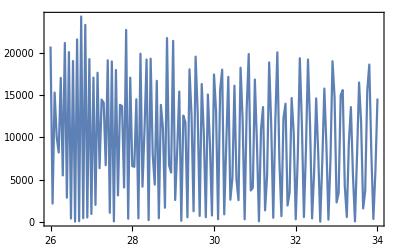

```mathematica
ListLinePlot[tk06s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk06sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,26,34,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.74054×10^7}. NIntegrate obtained 2320.27+1980.59 ⅈ and 169.011 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.66333×10^7}. NIntegrate obtained -3695.83+1781.54 ⅈ and 225.013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.06812×10^7}. NIntegrate obtained -704.825-118.48 ⅈ and 172.016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.58913×10^6}. NIntegrate obtained -1565.67-9.97364 ⅈ and 228.682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.45081×10^7}. NIntegrate obtained -2092.3+146.572 ⅈ and 174.932 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.00366×10^7}. NIntegrate obtained 1239.9-2840.41 ⅈ and 232.501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.41598×10^6}. NIntegrate obtained -1391.48-8.32261 ⅈ and 290.972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.98193×10^6}. NIntegrate obtained -2924.84-2934.4 ⅈ and 372.315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.97517×10^7}. NIntegrate obtained 1819.57-3183.61 ⅈ and 295.541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.73042×10^7}. NIntegrate obtained -1244.74-2709.04 ⅈ and 377.534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.39009×10^7}. NIntegrate obtained 1267.71+775.286 ⅈ and 383.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.07824×10^7}. NIntegrate obtained 2730.52-2371.16 ⅈ and 300.149 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.12059×10^7}. NIntegrate obtained 1192.46-2688.51 ⅈ and 470.182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.88073×10^6}. NIntegrate obtained 1942.17-1949.23 ⅈ and 477.063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.12059×10^7}. NIntegrate obtained 31.0113+1523.74 ⅈ and 483.722 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.08836×10^7}. NIntegrate obtained 777.887-3957.05 ⅈ and 588.528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.05613×10^7}. NIntegrate obtained 2092.91+486.003 ⅈ and 595.713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.81551×10^6}. NIntegrate obtained 343.62+4683.89 ⅈ and 602.336 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.67345×10^7}. NIntegrate obtained 3253.63-4278.48 ⅈ and 727.962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.2263×10^7}. NIntegrate obtained 2965.39-602.476 ⅈ and 736.734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.76754×10^6}. NIntegrate obtained 1527.53-409.797 ⅈ and 892.22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.82712×10^7}. NIntegrate obtained -781.956+1985.4 ⅈ and 747.096 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.50328×10^7}. NIntegrate obtained 1306.39+3375.7 ⅈ and 903.434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.50328×10^7}. NIntegrate obtained -877.083+3870.09 ⅈ and 914.648 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0239×10^7}. NIntegrate obtained 1655.01+1740.83 ⅈ and 1083.11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 48.6766+3902.68 ⅈ and 1096.28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.13522×10^7}. NIntegrate obtained 342.026+558.759 ⅈ and 1303.58 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained -1533.95+2488.56 ⅈ and 1109.72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.36985×10^7}. NIntegrate obtained -2635.05+1320.97 ⅈ and 1318.39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {505190.}. NIntegrate obtained -4060.43-1269.7 ⅈ and 1314.63 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 27290.6
26.05 | 3835.39
26.1 | 22636.9
26.15 | 10838.9
26.2 | 12507.4
26.25 | 16241.5
26.3 | 5720.22
26.35 | 22851.1
26.4 | 1725.37
26.45 | 26510.5
26.5 | 263.455
26.55 | 29072.4
26.6 | 339.21
26.65 | 26986.5
26.7 | 445.892
26.75 | 24480.3
26.8 | 266.198
26.85 | 24986.3
26.9 | 130.301
26.95 | 26923.2
27. | 1005.37
27.05 | 26017.8
27.1 | 4554.63
27.15 | 19768.4
27.2 | 8989.17
27.25 | 13602.3
27.3 | 13504.7
27.35 | 8931.29
27.4 | 20695.2
27.45 | 2857.95
27.5 | 27483.2
27.55 | 164.217
27.6 | 24928.1
27.65 | 6585.46
27.7 | 13390.
27.75 | 15726.7
27.8 | 4120.3
27.85 | 22874.6
27.9 | 283.231
27.95 | 23969.1
28. | 7470.77
28.05 | 11291.1
28.1 | 23623.5
28.15 | 155.01
28.2 | 24458.6
28.25 | 6809.14
28.3 | 9862.68
28.35 | 18987.3
28.4 | 534.679
28.45 | 23374.8
28.5 | 7487.25
28.55 | 8911.24
28.6 | 25984.3
28.65 | 907.022
28.7 | 18872.7
28.75 | 17477.9
28.8 | 845.475
28.85 | 22359.7
28.9 | 7176.47
28.95 | 6699.81
29. | 22672.3
29.05 | 1567.48
29.1 | 14796.7
29.15 | 22597.3
29.2 | 141.824
29.25 | 19013.8
29.3 | 20005.6
29.35 | 138.127
29.4 | 18923.2
29.45 | 14827.7
29.5 | 1056.54
29.55 | 20206.
29.6 | 11921.8
29.65 | 2005.19
29.7 | 23676.
29.75 | 13637.1
29.8 | 1257.03
29.85 | 23799.
29.9 | 16111.6
29.95 | 216.986
30. | 19051.1
30.05 | 16161.
30.1 | 372.669
30.15 | 15713.4
30.2 | 17452.1
30.25 | 319.683
30.3 | 14534.6
30.35 | 23231.9
30.4 | 2825.57
30.45 | 8916.86
30.5 | 25926.8
30.55 | 9883.06
30.6 | 1650.39
30.65 | 20484.4
30.7 | 15174.
30.75 | 379.783
30.8 | 13400.8
30.85 | 19683.6
30.9 | 2381.09
30.95 | 7533.11
31. | 24194.7
31.05 | 12226.5
31.1 | 317.125
31.15 | 18200.2
31.2 | 23344.4
31.25 | 3975.86
31.3 | 4536.07
31.35 | 21031.4
31.4 | 13884.9
31.45 | 305.507
31.5 | 12205.9
31.55 | 20462.5
31.6 | 5769.65
31.65 | 2361.7
31.7 | 20234.9
31.75 | 20824.2
31.8 | 2630.98
31.85 | 5544.14
31.9 | 23015.7
31.95 | 18316.8
32. | 1513.45
32.05 | 6453.81
32.1 | 20598.3
32.15 | 12919.
32.2 | 452.791
32.25 | 9652.41
32.3 | 21029.1
32.35 | 10925.7
32.4 | 80.331
32.45 | 11965.5
32.5 | 24743.9
32.55 | 13618.1
32.6 | 127.23
32.65 | 9750.47
32.7 | 23250.7
32.75 | 15312.3
32.8 | 1092.65
32.85 | 5908.31
32.9 | 18918.5
32.95 | 14772.2
33. | 1613.94
33.05 | 5002.69
33.1 | 19325.2
33.15 | 18281.
33.2 | 3694.89
33.25 | 2181.08
33.3 | 17439.9
33.35 | 23980.3
33.4 | 11043.9
33.45 | 62.4281
33.5 | 8555.83
33.55 | 21125.
33.6 | 16436.4
33.65 | 2716.88
33.7 | 2697.21
33.75 | 15199.6
33.8 | 18329.9
33.85 | 6746.65
33.9 | 331.984
33.95 | 10720.9
34. | 22248.8)

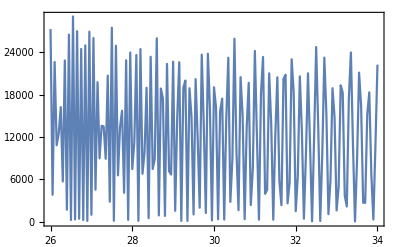

```mathematica
ListLinePlot[tk06sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk03s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,73,77,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 59076.4+400870. ⅈ and 4419.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 141880.+284706. ⅈ and 4496.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -351919.+213976. ⅈ and 4763.11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -339398.-244795. ⅈ and 4493.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -212673.+247827. ⅈ and 4646.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained -319210.-102228. ⅈ and 4659.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 387524.+248513. ⅈ and 4906.42 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -79387.4+457995. ⅈ and 4819.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -456396.+105716. ⅈ and 4770.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.12884×10^7}. NIntegrate obtained 472748.-130462. ⅈ and 2065.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.92457×10^7}. NIntegrate obtained 303984.+385444. ⅈ and 2276.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.46731×10^7}. NIntegrate obtained -243541.+435566. ⅈ and 2456.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 227160.-441911. ⅈ and 5822.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 494840.+38607.8 ⅈ and 5788.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 155354.+470553. ⅈ and 5767.52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -167399.-450116. ⅈ and 5467.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 347940.-326224. ⅈ and 5422.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 432376.+193009. ⅈ and 5373.29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -404193.-163036. ⅈ and 4962.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -5758.41-429900. ⅈ and 4905.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 388826.-169040. ⅈ and 4855.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -335078.+155714. ⅈ and 4434.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -267237.-244465. ⅈ and 4375.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 120240.-333689. ⅈ and 4323.68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(73. | 19458.4
73.05 | 18868.3
73.1 | 18118.5
73.15 | 17227.1
73.2 | 16260.5
73.25 | 15231.
73.3 | 14172.5
73.35 | 13151.1
73.4 | 12177.6
73.45 | 11308.9
73.5 | 10512.8
73.55 | 9896.93
73.6 | 9418.13
73.65 | 9131.6
73.7 | 9011.71
73.75 | 9053.89
73.8 | 9284.87
73.85 | 9647.77
73.9 | 10100.8
73.95 | 10748.8
74. | 11428.4
74.05 | 12147.4
74.1 | 12919.4
74.15 | 13640.5
74.2 | 14313.7
74.25 | 14953.6
74.3 | 15487.9
74.35 | 15851.5
74.4 | 16094.9
74.45 | 16181.9
74.5 | 16099.2
74.55 | 15907.8
74.6 | 15456.1
74.65 | 15197.2
74.7 | 14256.
74.75 | 13431.2
74.8 | 12522.8
74.85 | 11517.5
74.9 | 10445.9
74.95 | 9352.9
75. | 8236.4
75.05 | 7137.1
75.1 | 6081.92
75.15 | 5071.42
75.2 | 4142.28
75.25 | 3305.96
75.3 | 2561.38
75.35 | 1927.82
75.4 | 1407.81
75.45 | 992.873
75.5 | 688.933
75.55 | 487.27
75.6 | 374.164
75.65 | 344.326
75.7 | 381.77
75.75 | 467.473
75.8 | 603.303
75.85 | 757.35
75.9 | 923.259
75.95 | 1089.84
76. | 1239.26
76.05 | 1367.88
76.1 | 1468.88
76.15 | 1530.42
76.2 | 1557.14
76.25 | 1547.04
76.3 | 1494.95
76.35 | 1413.52
76.4 | 1302.95
76.45 | 1166.65
76.5 | 1023.07
76.55 | 866.746
76.6 | 713.907
76.65 | 572.618
76.7 | 450.356
76.75 | 352.85
76.8 | 284.473
76.85 | 252.834
76.9 | 258.187
76.95 | 304.378
77. | 390.525)

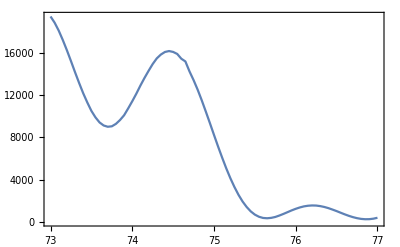

```mathematica
ListLinePlot[tk03s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk03sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,73,77,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.86874×10^6}. NIntegrate obtained -79448.8-150420. ⅈ and 3889.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.32677×10^6}. NIntegrate obtained -29425.7-200472. ⅈ and 3746.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.11498×10^7}. NIntegrate obtained 109778.-134518. ⅈ and 3928.66 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.43695×10^7}. NIntegrate obtained 175823.-105972. ⅈ and 3606.14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.11498×10^7}. NIntegrate obtained 169946.+49679.4 ⅈ and 3941.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.05426×10^7}. NIntegrate obtained 167446.+123562. ⅈ and 3729.76 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained -187315.-132299. ⅈ and 3662.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.06251×10^7}. NIntegrate obtained -243028.+57340.2 ⅈ and 4035.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 50604.6-226987. ⅈ and 4166.21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.06251×10^7}. NIntegrate obtained -147094.-202165. ⅈ and 4225. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.91632×10^7}. NIntegrate obtained 229846.-40604.9 ⅈ and 4324.94 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94596×10^6}. NIntegrate obtained 127560.-213464. ⅈ and 4441.39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.63934×10^7}. NIntegrate obtained -113518.+219197. ⅈ and 5194.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.25666×10^7}. NIntegrate obtained 77571.9+213355. ⅈ and 4899.27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.25666×10^7}. NIntegrate obtained -165691.+151829. ⅈ and 4855.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.63934×10^7}. NIntegrate obtained -244927.-19175.6 ⅈ and 5154.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.27503×10^7}. NIntegrate obtained -201704.-93537. ⅈ and 4824.63 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.93469×10^7}. NIntegrate obtained -76243.3-231521. ⅈ and 5121.05 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.23455×10^7}. NIntegrate obtained 186023.+84356.1 ⅈ and 4435.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.54189×10^7}. NIntegrate obtained -6153.95+201805. ⅈ and 4402.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.54189×10^7}. NIntegrate obtained -186590.+71248.5 ⅈ and 4332.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.52165×10^7}. NIntegrate obtained 164226.-70037.5 ⅈ and 3954.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.52165×10^7}. NIntegrate obtained 126191.+121742. ⅈ and 3917. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -61576.3+160702. ⅈ and 3874.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(73. | 3858.68
73.05 | 3397.
73.1 | 2917.83
73.15 | 2452.34
73.2 | 2026.82
73.25 | 1681.89
73.3 | 1434.24
73.35 | 1311.83
73.4 | 1340.69
73.45 | 1507.91
73.5 | 1837.38
73.55 | 2320.87
73.6 | 2947.9
73.65 | 3699.77
73.7 | 4551.91
73.75 | 5474.74
73.8 | 6439.74
73.85 | 7419.68
73.9 | 8335.49
73.95 | 9192.48
74. | 9979.46
74.05 | 10597.2
74.1 | 11062.7
74.15 | 11308.8
74.2 | 11430.5
74.25 | 11309.5
74.3 | 10997.1
74.35 | 10479.2
74.4 | 9817.15
74.45 | 8976.74
74.5 | 8031.36
74.55 | 6981.81
74.6 | 5876.81
74.65 | 4813.91
74.7 | 3747.37
74.75 | 2760.34
74.8 | 1898.42
74.85 | 1192.35
74.9 | 666.191
74.95 | 343.68
75. | 249.87
75.05 | 390.806
75.1 | 767.175
75.15 | 1365.56
75.2 | 2189.59
75.25 | 3195.78
75.3 | 4356.27
75.35 | 5659.86
75.4 | 7033.27
75.45 | 8453.27
75.5 | 9878.53
75.55 | 11255.6
75.6 | 12539.7
75.65 | 13702.
75.7 | 14700.2
75.75 | 15483.6
75.8 | 16057.6
75.85 | 16403.8
75.9 | 16470.6
75.95 | 16306.2
76. | 15889.4
76.05 | 15243.
76.1 | 14380.6
76.15 | 13344.5
76.2 | 12146.1
76.25 | 10832.1
76.3 | 9449.65
76.35 | 8038.93
76.4 | 6632.
76.45 | 5280.9
76.5 | 4031.5
76.55 | 2891.53
76.6 | 1924.17
76.65 | 1143.58
76.7 | 561.52
76.75 | 203.369
76.8 | 66.4022
76.85 | 152.413
76.9 | 453.115
76.95 | 950.291
77. | 1628.12)

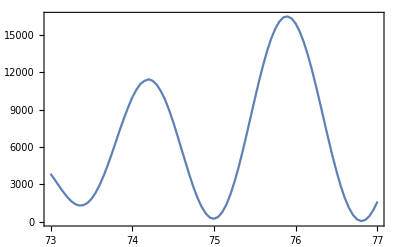

```mathematica
ListLinePlot[tk03sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk04s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,69,73,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.81325×10^7}. NIntegrate obtained 24050.6-81485.6 ⅈ and 662.458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.16035×10^6}. NIntegrate obtained 47260.6-86242. ⅈ and 953.433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.81325×10^7}. NIntegrate obtained 86681.4-10708.3 ⅈ and 623.688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.16035×10^6}. NIntegrate obtained 97644.3+9371.3 ⅈ and 1029.09 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.81325×10^7}. NIntegrate obtained 45507.3+77130.5 ⅈ and 592.012 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.34587×10^7}. NIntegrate obtained 29674.3+93019.1 ⅈ and 1105.56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained -56535.7-19324. ⅈ and 2502.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -32286.3-81253.3 ⅈ and 1775.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained -4254.55-55649.5 ⅈ and 2570.93 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 60902.7-59927.2 ⅈ and 1850.46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 45743.-23973. ⅈ and 2638.82 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 76932.4+31985.7 ⅈ and 1925.42 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -5358.02+7279.77 ⅈ and 2990.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -3623.97+1962.34 ⅈ and 3037.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -5062.06+4188.14 ⅈ and 3089.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 13972.2-65955.7 ⅈ and 3495.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 74191.9-15283.7 ⅈ and 3519.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 48480.3+68808.4 ⅈ and 3536.77 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -100860.-114813. ⅈ and 2989.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -239477.+3533.73 ⅈ and 1826.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 69834.4-145604. ⅈ and 2787.65 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -99847.6-227427. ⅈ and 2156.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 176613.-186781. ⅈ and 2541.43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 170397.+7602.07 ⅈ and 2427.03 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(69. | 4012.84
69.05 | 3441.89
69.1 | 3010.24
69.15 | 2728.9
69.2 | 2620.75
69.25 | 2710.9
69.3 | 2976.93
69.35 | 3421.73
69.4 | 4032.43
69.45 | 4761.54
69.5 | 5588.53
69.55 | 6475.76
69.6 | 7364.15
69.65 | 8222.82
69.7 | 9009.08
69.75 | 9673.47
69.8 | 10191.9
69.85 | 10534.6
69.9 | 10681.4
69.95 | 10628.1
70. | 10365.6
70.05 | 9910.14
70.1 | 9284.55
70.15 | 8501.11
70.2 | 7601.65
70.25 | 6628.35
70.3 | 5603.91
70.35 | 4579.89
70.4 | 3600.8
70.45 | 2690.76
70.5 | 1885.16
70.55 | 1218.74
70.6 | 698.582
70.65 | 339.926
70.7 | 148.889
70.75 | 114.589
70.8 | 229.177
70.85 | 471.018
70.9 | 813.267
70.95 | 1235.55
71. | 1698.
71.05 | 2168.67
71.1 | 2628.43
71.15 | 3035.31
71.2 | 3367.49
71.25 | 3619.87
71.3 | 3761.03
71.35 | 3794.08
71.4 | 3726.4
71.45 | 3551.18
71.5 | 3296.76
71.55 | 2984.1
71.6 | 2626.31
71.65 | 2268.28
71.7 | 1936.36
71.75 | 1654.97
71.8 | 1470.61
71.85 | 1400.67
71.9 | 1473.66
71.95 | 1716.45
72. | 2126.92
72.05 | 2723.22
72.1 | 3510.95
72.15 | 4474.81
72.2 | 5581.9
72.25 | 6850.79
72.3 | 8201.46
72.35 | 9641.78
72.4 | 11120.6
72.45 | 12596.8
72.5 | 14026.1
72.55 | 15384.8
72.6 | 16627.9
72.65 | 17702.2
72.7 | 18657.
72.75 | 19286.8
72.8 | 19779.3
72.85 | 20035.5
72.9 | 20061.1
72.95 | 19864.6
73. | 19458.4)

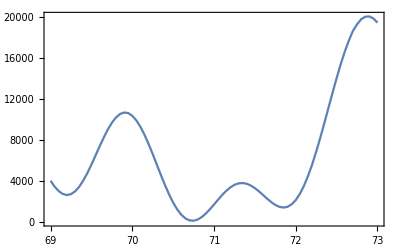

```mathematica
ListLinePlot[tk04s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk04sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,69,73,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18433×10^6}. NIntegrate obtained -7088.62+45169. ⅈ and 981.697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.20793×10^7}. NIntegrate obtained -32155.1+44789.6 ⅈ and 1466.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.20793×10^7}. NIntegrate obtained -54665.9-12606.2 ⅈ and 1520.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18433×10^6}. NIntegrate obtained -45218.3+10399.8 ⅈ and 984.545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.20793×10^7}. NIntegrate obtained -9956.09-55996. ⅈ and 1598.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18433×10^6}. NIntegrate obtained -26921.3-38464.3 ⅈ and 1007.35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.23757×10^6}. NIntegrate obtained 17016.3+53072.5 ⅈ and 2155.52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.03776×10^7}. NIntegrate obtained -40800.2+36035.1 ⅈ and 2229.26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.03776×10^7}. NIntegrate obtained -47969.6-22210.3 ⅈ and 2305.37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.89796×10^7}. NIntegrate obtained 30617.5+9834.72 ⅈ and 2818.28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.12323×10^7}. NIntegrate obtained 2305.97+28834. ⅈ and 2874.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.46395×10^6}. NIntegrate obtained -22866.9+11510. ⅈ and 2932.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.95795×10^6}. NIntegrate obtained 2724.71+6161.16 ⅈ and 3127.16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.37623×10^7}. NIntegrate obtained -7579.03+3630.3 ⅈ and 3174.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained 3325.07+34057.9 ⅈ and 3338.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained -33682.1+16723.2 ⅈ and 3361.14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.75555×10^6}. NIntegrate obtained -6293.4-8728.21 ⅈ and 3122.85 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained -30463.6-27876.1 ⅈ and 3348.73 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.77953×10^6}. NIntegrate obtained 51025.5+57921.7 ⅈ and 2851.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.77953×10^6}. NIntegrate obtained -36621.5+73995. ⅈ and 2682.41 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.44894×10^7}. NIntegrate obtained 130975.+330.56 ⅈ and 3475.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained -87739.5-5491.42 ⅈ and 2609.65 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.44894×10^7}. NIntegrate obtained 53046.+124901. ⅈ and 3554.46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.44894×10^7}. NIntegrate obtained -97615.7+101443. ⅈ and 3568.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(69. | 3667.19
69.05 | 2675.87
69.1 | 1847.1
69.15 | 1227.35
69.2 | 841.749
69.25 | 709.696
69.3 | 833.757
69.35 | 1200.02
69.4 | 1784.86
69.45 | 2543.43
69.5 | 3437.26
69.55 | 4410.66
69.6 | 5396.22
69.65 | 6350.9
69.7 | 7211.98
69.75 | 7928.27
69.8 | 8461.85
69.85 | 8782.31
69.9 | 8867.98
69.95 | 8715.71
70. | 8331.32
70.05 | 7736.85
70.1 | 6966.71
70.15 | 6054.16
70.2 | 5054.1
70.25 | 4025.81
70.3 | 3012.51
70.35 | 2075.34
70.4 | 1271.91
70.45 | 639.097
70.5 | 215.319
70.55 | 30.7158
70.6 | 97.9505
70.65 | 421.226
70.7 | 987.556
70.75 | 1778.8
70.8 | 2765.37
70.85 | 3900.68
70.9 | 5137.13
70.95 | 6430.35
71. | 7716.18
71.05 | 8938.74
71.1 | 10056.8
71.15 | 11018.5
71.2 | 11778.4
71.25 | 12314.8
71.3 | 12608.1
71.35 | 12645.
71.4 | 12402.5
71.45 | 11964.9
71.5 | 11282.8
71.55 | 10414.3
71.6 | 9392.75
71.65 | 8266.49
71.7 | 7083.18
71.75 | 5886.79
71.8 | 4722.94
71.85 | 3637.45
71.9 | 2667.13
71.95 | 1844.1
72. | 1193.7
72.05 | 724.406
72.1 | 447.392
72.15 | 359.732
72.2 | 448.077
72.25 | 691.781
72.3 | 1064.84
72.35 | 1541.43
72.4 | 2084.
72.45 | 2653.86
72.5 | 3220.9
72.55 | 3751.03
72.6 | 4216.08
72.65 | 4579.38
72.7 | 4857.68
72.75 | 4952.33
72.8 | 4965.54
72.85 | 4837.54
72.9 | 4608.79
72.95 | 4271.41
73. | 3858.68)

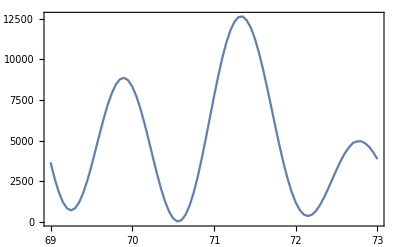

```mathematica
ListLinePlot[tk04sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk05s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/30,0]},{x,77,81,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 224922.+200202. ⅈ and 3935.83 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 96680.8+190729. ⅈ and 3312.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -95865.+277214. ⅈ and 3876.89 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -133498.+156217. ⅈ and 3248.41 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -187966.-60352.4 ⅈ and 3188.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -284905.+17351.9 ⅈ and 3823.66 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 126063.+37069.6 ⅈ and 2659.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 13328.3+122886. ⅈ and 2678.54 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -100712.+55832. ⅈ and 2651.15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 44928.7-25898.9 ⅈ and 2248. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 35103.1+27111.5 ⅈ and 2195.14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -9813.2+35727.8 ⅈ and 2140.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -1287.98+15940.3 ⅈ and 1697.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -20903.6+6116.74 ⅈ and 1640.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -16814.-21585.6 ⅈ and 1584.01 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 37680.7+52963.6 ⅈ and 1096.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -36819.1+58239.5 ⅈ and 1028.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -71538.7-12678. ⅈ and 960.976 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 94882.3+20215.6 ⅈ and 544.038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 17644.8+97866.9 ⅈ and 505.687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -85855.1+54636.1 ⅈ and 469.783 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained 99465.6-59458.2 ⅈ and 361.385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained 93784.6+70075. ⅈ and 389.902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained -29346.5+114434. ⅈ and 436.275 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(77. | 390.525
77.05 | 512.78
77.1 | 667.454
77.15 | 853.688
77.2 | 1059.44
77.25 | 1280.27
77.3 | 1513.1
77.35 | 1742.02
77.4 | 1962.85
77.45 | 2168.33
77.5 | 2346.4
77.55 | 2495.54
77.6 | 2612.69
77.65 | 2686.37
77.7 | 2712.44
77.75 | 2704.01
77.8 | 2647.35
77.85 | 2548.01
77.9 | 2407.06
77.95 | 2230.27
78. | 2032.05
78.05 | 1808.1
78.1 | 1560.09
78.15 | 1318.65
78.2 | 1077.37
78.25 | 835.282
78.3 | 618.327
78.35 | 427.055
78.4 | 260.452
78.45 | 134.589
78.5 | 48.312
78.55 | 5.13011
78.6 | 6.80485
78.65 | 53.0622
78.7 | 142.899
78.75 | 271.918
78.8 | 437.577
78.85 | 635.611
78.9 | 852.642
78.95 | 1092.82
79. | 1340.78
79.05 | 1593.04
79.1 | 1837.98
79.15 | 2070.19
79.2 | 2278.44
79.25 | 2462.92
79.3 | 2613.2
79.35 | 2724.09
79.4 | 2796.96
79.45 | 2825.02
79.5 | 2807.36
79.55 | 2750.1
79.6 | 2648.85
79.65 | 2509.43
79.7 | 2339.89
79.75 | 2138.35
79.8 | 1916.89
79.85 | 1683.21
79.9 | 1438.96
79.95 | 1198.23
80. | 967.377
80.05 | 750.644
80.1 | 560.59
80.15 | 400.806
80.2 | 276.616
80.25 | 195.799
80.3 | 158.993
80.35 | 170.534
80.4 | 231.554
80.45 | 340.06
80.5 | 497.896
80.55 | 699.307
80.6 | 940.668
80.65 | 1219.6
80.7 | 1526.1
80.75 | 1855.26
80.8 | 2201.4
80.85 | 2552.27
80.9 | 2902.88
80.95 | 3245.58
81. | 3568.88)

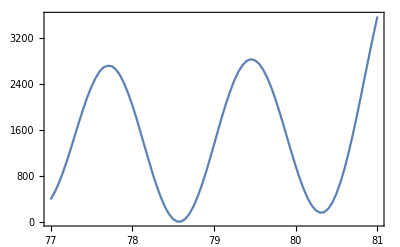

```mathematica
ListLinePlot[tk05s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk05sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/30,0]},{x,77,81,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.49954×10^7}. NIntegrate obtained -111226.-93231.2 ⅈ and 3548.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -49883.6-79910. ⅈ and 2992. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained 51647.2-73121. ⅈ and 2935.46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.49954×10^7}. NIntegrate obtained 40840.6-134666. ⅈ and 3501.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 83042.8+18815.8 ⅈ and 2890.35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 135391.-14240.8 ⅈ and 3455.27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -52189.5-12891. ⅈ and 2491.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -7050.22-49744.2 ⅈ and 2437.82 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -21410.+12297.9 ⅈ and 1955.94 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 40612.6-23718.4 ⅈ and 2391.55 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -17765.7-13308.4 ⅈ and 1899.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 4343.01-19341.1 ⅈ and 1853.98 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 5570.31+1002.58 ⅈ and 1388.88 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -5361.72-28474.7 ⅈ and 822.122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 4154.84+5884.49 ⅈ and 1323.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 25740.7-17920.1 ⅈ and 770.202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -3136.98+8459.71 ⅈ and 1246.63 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 28786.1+17298. ⅈ and 719.127 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.08275×10^7}. NIntegrate obtained -44570.3-16635.4 ⅈ and 522.212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4628×10^7}. NIntegrate obtained -43572.+29141.5 ⅈ and 577.693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained -43666.4-28526.7 ⅈ and 629.376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.25853×10^7}. NIntegrate obtained -2689.58-48683.3 ⅈ and 510.951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained 9056.21-50978.4 ⅈ and 675.873 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4628×10^7}. NIntegrate obtained 44422.2-22371.8 ⅈ and 504.341 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(77. | 1628.12
77.05 | 2453.4
77.1 | 3402.99
77.15 | 4433.12
77.2 | 5517.91
77.25 | 6608.04
77.3 | 7681.54
77.35 | 8691.69
77.4 | 9604.95
77.45 | 10408.
77.5 | 11051.
77.55 | 11533.6
77.6 | 11822.5
77.65 | 11939.8
77.7 | 11857.4
77.75 | 11580.7
77.8 | 11131.8
77.85 | 10519.7
77.9 | 9766.09
77.95 | 8890.81
78. | 7929.72
78.05 | 6912.39
78.1 | 5859.34
78.15 | 4819.98
78.2 | 3813.96
78.25 | 2875.63
78.3 | 2039.29
78.35 | 1318.52
78.4 | 741.054
78.45 | 323.631
78.5 | 74.1192
78.55 | 0.78841
78.6 | 103.795
78.65 | 377.67
78.7 | 815.586
78.75 | 1399.48
78.8 | 2111.22
78.85 | 2934.21
78.9 | 3833.11
78.95 | 4787.91
79. | 5767.94
79.05 | 6745.14
79.1 | 7691.67
79.15 | 8573.76
79.2 | 9372.97
79.25 | 10064.2
79.3 | 10625.2
79.35 | 11050.6
79.4 | 11312.1
79.45 | 11422.
79.5 | 11370.3
79.55 | 11153.4
79.6 | 10785.2
79.65 | 10280.7
79.7 | 9643.24
79.75 | 8900.5
79.8 | 8075.83
79.85 | 7185.32
79.9 | 6256.73
79.95 | 5319.09
80. | 4393.73
80.05 | 3506.89
80.1 | 2683.1
80.15 | 1942.62
80.2 | 1303.9
80.25 | 784.727
80.3 | 396.175
80.35 | 145.972
80.4 | 39.711
80.45 | 77.7526
80.5 | 256.189
80.55 | 568.449
80.6 | 1002.82
80.65 | 1546.48
80.7 | 2180.9
80.75 | 2886.73
80.8 | 3646.82
80.85 | 4434.15
80.9 | 5227.65
80.95 | 6008.79
81. | 6750.55)

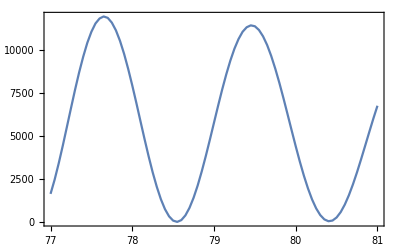

```mathematica
ListLinePlot[tk05sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
llts1=AmplTwistTab[1,73/mee,73/mee/30];
lltsm1=AmplTwistTab[-1,73/mee,73/mee/30];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 141880.+284706. ⅈ and 4496.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71018×10^7}. NIntegrate obtained 290120.-160044. ⅈ and 4500.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 170250.+268746. ⅈ and 4487.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.2098×10^7}. NIntegrate obtained 274281.-188443. ⅈ and 4364.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained 196872.+250069. ⅈ and 4500.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34774×10^7}. NIntegrate obtained 255608.-215059. ⅈ and 4363.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained -154519.-308149. ⅈ and 4637.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.30088×10^7}. NIntegrate obtained -302759.+136227. ⅈ and 4506.18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.67532×10^7}. NIntegrate obtained -182876.-292351. ⅈ and 4514.58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61911×10^7}. NIntegrate obtained -286782.+164678. ⅈ and 4634.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.11238×10^6}. NIntegrate obtained -209544.-273681. ⅈ and 4502.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.93844×10^7}. NIntegrate obtained -268139.+191347. ⅈ and 4634.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 141880.+284706. ⅈ and 4496.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71018×10^7}. NIntegrate obtained 290120.-160044. ⅈ and 4500.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 170250.+268746. ⅈ and 4487.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.2098×10^7}. NIntegrate obtained 274281.-188443. ⅈ and 4364.08 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained 196872.+250069. ⅈ and 4500.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34774×10^7}. NIntegrate obtained 255608.-215059. ⅈ and 4363.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.35599×10^7}. NIntegrate obtained -154519.-308149. ⅈ and 4637.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.30088×10^7}. NIntegrate obtained -302759.+136227. ⅈ and 4506.18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.67532×10^7}. NIntegrate obtained -182876.-292351. ⅈ and 4514.58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61911×10^7}. NIntegrate obtained -286782.+164678. ⅈ and 4634.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.11238×10^6}. NIntegrate obtained -209544.-273681. ⅈ and 4502.08 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.93844×10^7}. NIntegrate obtained -268139.+191347. ⅈ and 4634.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.12323×10^7}. NIntegrate obtained -84518.7-153468. ⅈ and 3937.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.86874×10^6}. NIntegrate obtained -79448.8-150420. ⅈ and 3889.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.11498×10^7}. NIntegrate obtained -79761.2-150318. ⅈ and 3928.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.79676×10^7}. NIntegrate obtained -84650.7-153903. ⅈ and 3940.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.80352×10^6}. NIntegrate obtained -80070.2-150140. ⅈ and 3860.96 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.16932×10^7}. NIntegrate obtained -84773.7-154305. ⅈ and 3946.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.80501×10^7}. NIntegrate obtained -82041.9-158860. ⅈ and 3950.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.81325×10^7}. NIntegrate obtained -76597.7-155883. ⅈ and 3898.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.10673×10^7}. NIntegrate obtained -76519.9-155499. ⅈ and 3899.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.80501×10^7}. NIntegrate obtained -81641.9-158895. ⅈ and 3915.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.10673×10^7}. NIntegrate obtained -76466.-155099. ⅈ and 3897.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained -81230.9-158965. ⅈ and 3987.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.86874×10^6}. NIntegrate obtained -79448.8-150420. ⅈ and 3889.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.12323×10^7}. NIntegrate obtained -84518.7-153468. ⅈ and 3937.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.11498×10^7}. NIntegrate obtained -79761.2-150318. ⅈ and 3928.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.79676×10^7}. NIntegrate obtained -84650.7-153903. ⅈ and 3940.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.80352×10^6}. NIntegrate obtained -80070.2-150140. ⅈ and 3860.96 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.16932×10^7}. NIntegrate obtained -84773.7-154305. ⅈ and 3946.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.80501×10^7}. NIntegrate obtained -82041.9-158860. ⅈ and 3950.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.81325×10^7}. NIntegrate obtained -76597.7-155883. ⅈ and 3898.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.80501×10^7}. NIntegrate obtained -81641.9-158895. ⅈ and 3915.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.10673×10^7}. NIntegrate obtained -76519.9-155499. ⅈ and 3899.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained -81230.9-158965. ⅈ and 3987.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.10673×10^7}. NIntegrate obtained -76466.-155099. ⅈ and 3897.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

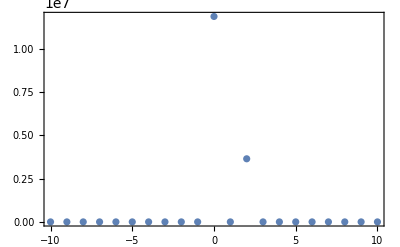
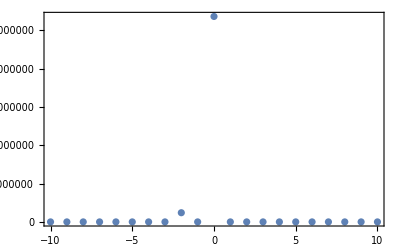

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
51.939017518112045
```

```mathematica
tk07s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,49,53,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -6299.03+2595.4 ⅈ and 61005.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 7388.68-11418.2 ⅈ and 56948.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -4181.26-2396.37 ⅈ and 59787.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 14575.1-1404.47 ⅈ and 55619. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -1471.18-2337.33 ⅈ and 60791.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 10783.2+11464.4 ⅈ and 53586.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -17753.3-3480.76 ⅈ and 48540.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -6916.42-18052. ⅈ and 44783.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 10262.7-16095.9 ⅈ and 40731.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 3133.01+5590.23 ⅈ and 41716.1 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -3396.52+1563.54 ⅈ and 47307.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 2202.1-5845.48 ⅈ and 38874.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 9976.11+21872.8 ⅈ and 35818.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -13308.4+21740.8 ⅈ and 34647.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -23373.1-2230.32 ⅈ and 33444.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 5352.16+2089.13 ⅈ and 22832.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -911.992+7392.2 ⅈ and 21508.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -10788.1-489.039 ⅈ and 20268.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained 23231.6-14061.5 ⅈ and 10863.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.4287×10^7}. NIntegrate obtained 22270.9+13051.5 ⅈ and 11103.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18433×10^6}. NIntegrate obtained -42.09+25027.3 ⅈ and 10339.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.54827×10^7}. NIntegrate obtained 4957.18-6357.33 ⅈ and 11286.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21358×10^6}. NIntegrate obtained 9361.49+5067.38 ⅈ and 12225.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.34587×10^7}. NIntegrate obtained -2233.93+12914.2 ⅈ and 13193. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(49. | 252.129
49.05 | 215.786
49.1 | 168.194
49.15 | 115.704
49.2 | 78.1098
49.25 | 51.3001
49.3 | 47.9597
49.35 | 64.8813
49.4 | 106.975
49.45 | 157.063
49.5 | 216.383
49.55 | 275.161
49.6 | 325.28
49.65 | 353.405
49.7 | 362.271
49.75 | 350.33
49.8 | 313.337
49.85 | 263.559
49.9 | 203.56
49.95 | 146.387
50. | 101.107
50.05 | 70.2219
50.1 | 60.3059
50.15 | 67.5166
50.2 | 96.114
50.25 | 141.774
50.3 | 189.56
50.35 | 238.574
50.4 | 276.475
50.45 | 300.367
50.5 | 313.174
50.55 | 301.977
50.6 | 276.099
50.65 | 242.751
50.7 | 183.368
50.75 | 134.382
50.8 | 89.9959
50.85 | 56.7704
50.9 | 30.3154
50.95 | 21.6607
51. | 30.212
51.05 | 51.3972
51.1 | 75.5384
51.15 | 113.197
51.2 | 145.271
51.25 | 163.736
51.3 | 181.004
51.35 | 183.979
51.4 | 171.532
51.45 | 148.44
51.5 | 128.497
51.55 | 93.2482
51.6 | 59.8849
51.65 | 34.4269
51.7 | 13.924
51.75 | 2.84467
51.8 | 2.08426
51.85 | 11.1491
51.9 | 25.2034
51.95 | 47.1942
52. | 67.1864
52.05 | 86.2507
52.1 | 103.179
52.15 | 108.262
52.2 | 107.252
52.25 | 100.504
52.3 | 85.3721
52.35 | 65.7103
52.4 | 45.936
52.45 | 26.601
52.5 | 10.6079
52.55 | 1.93082
52.6 | 0.480563
52.65 | 7.50545
52.7 | 21.8113
52.75 | 41.2309
52.8 | 65.6323
52.85 | 90.7636
52.9 | 112.379
52.95 | 129.975
53. | 141.942)

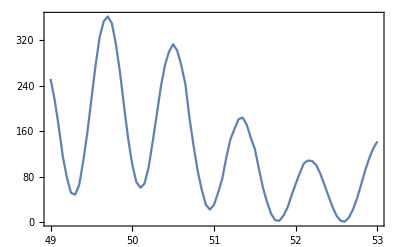

```mathematica
ListLinePlot[tk07s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,49,53,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.91671×10^6}. NIntegrate obtained 13864.3+33582.1 ⅈ and 60086. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.27877×10^7}. NIntegrate obtained 36132.7-3329.33 ⅈ and 61269.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71958×10^6}. NIntegrate obtained -25367.3+28489.1 ⅈ and 61902.2 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.40208×10^7}. NIntegrate obtained 18282.4+26447.2 ⅈ and 58166. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.61911×10^7}. NIntegrate obtained -39998.8-7190.38 ⅈ and 58603.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.40208×10^7}. NIntegrate obtained -12396.9+26382.5 ⅈ and 59637.6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.52352×10^7}. NIntegrate obtained 10470.9-996.327 ⅈ and 59709.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.91258×10^7}. NIntegrate obtained 135.894+13430.8 ⅈ and 57304.3 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.08275×10^7}. NIntegrate obtained -15133.5-977.411 ⅈ and 51566.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.5299×10^7}. NIntegrate obtained 37005.7-21149.4 ⅈ and 43580.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.71958×10^6}. NIntegrate obtained 34079.+20676.6 ⅈ and 42251.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.00179×10^7}. NIntegrate obtained -3507.4+38130.2 ⅈ and 39500. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.17234×10^6}. NIntegrate obtained 18225.3-2259.63 ⅈ and 30966.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained 12967.+20425.4 ⅈ and 28472.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.44707×10^7}. NIntegrate obtained -13530.1+26203.1 ⅈ and 27622.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.7323×10^7}. NIntegrate obtained -4584.54-26458.2 ⅈ and 20089.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.76453×10^7}. NIntegrate obtained 9912.83-15649.4 ⅈ and 19432.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.67158×10^7}. NIntegrate obtained 18245.1+2084.98 ⅈ and 18518.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.5805×10^7}. NIntegrate obtained 6978.15-28190.2 ⅈ and 16220.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.15359×10^7}. NIntegrate obtained 29939.1-9787.24 ⅈ and 16717.6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.47292×10^7}. NIntegrate obtained -11449.7+5554.36 ⅈ and 21723.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.15359×10^7}. NIntegrate obtained 22295.3+23158. ⅈ and 17118.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -7988.19-1606.13 ⅈ and 22108.2 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -2450.19-421.977 ⅈ and 23155.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(49. | 251.116
49.05 | 232.443
49.1 | 186.73
49.15 | 138.092
49.2 | 88.7876
49.25 | 49.9233
49.3 | 22.7029
49.35 | 15.3077
49.4 | 28.0792
49.45 | 55.969
49.5 | 89.6014
49.55 | 126.527
49.6 | 162.862
49.65 | 183.599
49.7 | 195.968
49.75 | 179.279
49.8 | 150.407
49.85 | 118.14
49.9 | 85.3651
49.95 | 52.525
50. | 28.255
50.05 | 19.0798
50.1 | 30.0914
50.15 | 47.4279
50.2 | 87.2515
50.25 | 121.312
50.3 | 160.977
50.35 | 195.13
50.4 | 217.097
50.45 | 221.469
50.5 | 205.395
50.55 | 175.166
50.6 | 139.15
50.65 | 91.839
50.7 | 72.7634
50.75 | 25.3749
50.8 | 6.83783
50.85 | 5.07138
50.9 | 21.7052
50.95 | 52.049
51. | 103.672
51.05 | 152.395
51.1 | 203.041
51.15 | 248.358
51.2 | 290.319
51.25 | 290.175
51.3 | 287.291
51.35 | 265.501
51.4 | 214.131
51.45 | 173.962
51.5 | 123.655
51.55 | 73.3676
51.6 | 38.1077
51.65 | 5.94895
51.7 | 0.380263
51.75 | 15.2182
51.8 | 42.2328
51.85 | 86.9438
51.9 | 151.342
51.95 | 194.207
52. | 250.021
52.05 | 280.632
52.1 | 308.431
52.15 | 317.339
52.2 | 320.571
52.25 | 275.288
52.3 | 236.849
52.35 | 183.285
52.4 | 127.533
52.45 | 82.1149
52.5 | 45.4114
52.55 | 11.8322
52.6 | 0.426411
52.65 | 4.57278
52.7 | 27.8067
52.75 | 56.8467
52.8 | 102.695
52.85 | 151.492
52.9 | 193.722
52.95 | 233.552
53. | 242.549)

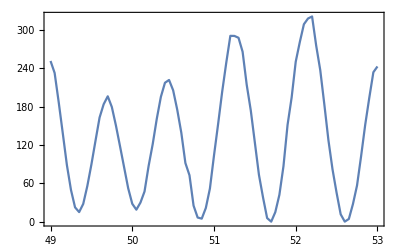

```mathematica
ListLinePlot[tk07sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk08s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/15,0]},{x,83,87,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 304625.-768143. ⅈ and 6151.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -58746.1-736508. ⅈ and 5254.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 832895.-7146.33 ⅈ and 6228.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 667929.-336688. ⅈ and 5339.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 322731.+774714. ⅈ and 6304.05 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 570698.+497189. ⅈ and 5424.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -292659.-833137. ⅈ and 6828.49 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 665546.-587196. ⅈ and 6948.63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 798229.+398194. ⅈ and 7017.86 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -796682.-462159. ⅈ and 6581.12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 129348.-915244. ⅈ and 7599.68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained 899477.-224330. ⅈ and 7661.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -926081.+169833. ⅈ and 7892.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -506003.-794621. ⅈ and 7951.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 547046.-767684. ⅈ and 8230.29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -589688.+728953. ⅈ and 8636.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -895299.-272140. ⅈ and 8684.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -83899.-929833. ⅈ and 8730.99 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 25246.7+906333. ⅈ and 8706.49 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -826792.+361257. ⅈ and 8192.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -642083.-627385. ⅈ and 8425.03 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 567101.+634189. ⅈ and 8198.98 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained -372757.+757108. ⅈ and 8099.23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -834757.-62034.9 ⅈ and 7995.84 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(83. | 21059.7
83.05 | 21468.1
83.1 | 21922.
83.15 | 22412.1
83.2 | 22936.4
83.25 | 23497.
83.3 | 24084.5
83.35 | 24697.1
83.4 | 25331.6
83.45 | 25982.6
83.5 | 26640.8
83.55 | 27301.
83.6 | 27961.3
83.65 | 28606.7
83.7 | 29237.2
83.75 | 29846.
83.8 | 30426.
83.85 | 30969.5
83.9 | 31476.4
83.95 | 31897.6
84. | 32312.2
84.05 | 32669.9
84.1 | 32939.8
84.15 | 33157.9
84.2 | 33316.3
84.25 | 33401.8
84.3 | 33411.9
84.35 | 33368.9
84.4 | 33240.2
84.45 | 33058.6
84.5 | 32816.6
84.55 | 32468.1
84.6 | 32132.9
84.65 | 31715.2
84.7 | 31231.2
84.75 | 30726.5
84.8 | 30173.8
84.85 | 29574.5
84.9 | 28972.4
84.95 | 28333.3
85. | 27671.8
85.05 | 27034.7
85.1 | 26347.4
85.15 | 25680.9
85.2 | 25036.3
85.25 | 24381.
85.3 | 23762.2
85.35 | 23151.7
85.4 | 22555.7
85.45 | 22000.5
85.5 | 21480.6
85.55 | 20973.4
85.6 | 20516.9
85.65 | 20093.1
85.7 | 19689.8
85.75 | 19339.4
85.8 | 19017.5
85.85 | 18716.3
85.9 | 18476.4
85.95 | 18233.1
86. | 18044.7
86.05 | 17853.4
86.1 | 17699.3
86.15 | 17566.2
86.2 | 17447.
86.25 | 17297.9
86.3 | 17194.
86.35 | 17088.5
86.4 | 16985.5
86.45 | 16870.9
86.5 | 16773.2
86.55 | 16651.2
86.6 | 16516.5
86.65 | 16372.3
86.7 | 16207.2
86.75 | 16064.7
86.8 | 15835.4
86.85 | 15565.4
86.9 | 15370.7
86.95 | 15098.
87. | 14814.8)

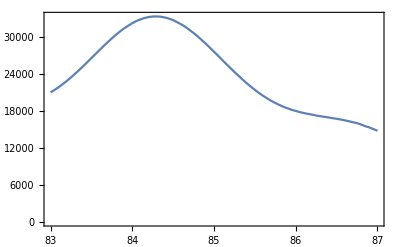

```mathematica
ListLinePlot[tk08s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk08sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/15,0]},{x,83,87,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.42232×10^7}. NIntegrate obtained 21095.3+337678. ⅈ and 5584.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.25853×10^7}. NIntegrate obtained -161517.+348952. ⅈ and 6523.83 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.42232×10^7}. NIntegrate obtained -309171.+147224. ⅈ and 5672.28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51718×10^6}. NIntegrate obtained -388150.-18742.2 ⅈ and 6605.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.42232×10^7}. NIntegrate obtained -254957.-234771. ⅈ and 5753.56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.51718×10^6}. NIntegrate obtained -129995.-370420. ⅈ and 6678.14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.84361×10^7}. NIntegrate obtained 120584.+402003. ⅈ and 6978.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0239×10^7}. NIntegrate obtained 371190.+223529. ⅈ and 7635.27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.90472×10^6}. NIntegrate obtained -328371.+265056. ⅈ and 7062.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {606389.}. NIntegrate obtained -66474.7+428425. ⅈ and 7591.67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.90472×10^6}. NIntegrate obtained -371394.-204619. ⅈ and 7258.44 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0239×10^7}. NIntegrate obtained -421246.+100213. ⅈ and 7830.67 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.99728×10^7}. NIntegrate obtained 418102.-76822.5 ⅈ and 8328.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.58237×10^7}. NIntegrate obtained 260589.-311896. ⅈ and 8608.96 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.19407×10^7}. NIntegrate obtained 227326.+357338. ⅈ and 8382.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.58237×10^7}. NIntegrate obtained 384745.+124984. ⅈ and 8633.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.58237×10^7}. NIntegrate obtained 27246.1+401924. ⅈ and 8597.42 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.19407×10^7}. NIntegrate obtained -244985.+343343. ⅈ and 8388.61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75254×10^7}. NIntegrate obtained 7582.8-388309. ⅈ and 8629.04 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.63037×10^6}. NIntegrate obtained -230822.-290601. ⅈ and 6191.66 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 362064.-136732. ⅈ and 8436.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.77953×10^6}. NIntegrate obtained 182313.-321367. ⅈ and 5943.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.08275×10^7}. NIntegrate obtained 364163.+48437. ⅈ and 5726.81 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 261229.+283203. ⅈ and 8322.93 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(83. | 4971.41
83.05 | 5159.51
83.1 | 5323.45
83.15 | 5458.92
83.2 | 5565.14
83.25 | 5643.33
83.3 | 5685.7
83.35 | 5697.96
83.4 | 5675.24
83.45 | 5622.88
83.5 | 5535.59
83.55 | 5419.25
83.6 | 5275.63
83.65 | 5104.48
83.7 | 4905.76
83.75 | 4701.15
83.8 | 4473.68
83.85 | 4232.13
83.9 | 3986.55
83.95 | 3744.45
84. | 3493.85
84.05 | 3272.65
84.1 | 3047.43
84.15 | 2843.6
84.2 | 2662.08
84.25 | 2510.46
84.3 | 2396.82
84.35 | 2311.5
84.4 | 2264.05
84.45 | 2259.63
84.5 | 2303.87
84.55 | 2398.77
84.6 | 2539.03
84.65 | 2712.05
84.7 | 2936.69
84.75 | 3208.02
84.8 | 3520.03
84.85 | 3867.89
84.9 | 4261.39
84.95 | 4678.67
85. | 5122.02
85.05 | 5592.57
85.1 | 6076.37
85.15 | 6573.38
85.2 | 7074.9
85.25 | 7575.39
85.3 | 8070.84
85.35 | 8554.03
85.4 | 9008.87
85.45 | 9449.5
85.5 | 9856.3
85.55 | 10222.1
85.6 | 10554.3
85.65 | 10846.8
85.7 | 11070.9
85.75 | 11255.9
85.8 | 11390.7
85.85 | 11460.3
85.9 | 11479.3
85.95 | 11436.8
86. | 11346.1
86.05 | 11201.
86.1 | 11003.1
86.15 | 10757.1
86.2 | 10474.6
86.25 | 10126.4
86.3 | 9754.83
86.35 | 9354.27
86.4 | 8923.64
86.45 | 8500.68
86.5 | 7970.61
86.55 | 7475.5
86.6 | 6984.25
86.65 | 6488.39
86.7 | 5999.36
86.75 | 5524.34
86.8 | 5076.68
86.85 | 4644.5
86.9 | 4248.25
86.95 | 3872.63
87. | 3530.94)

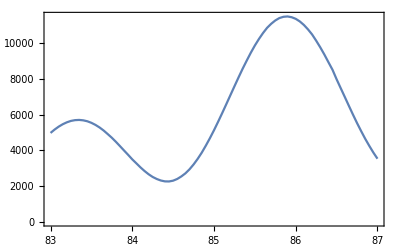

```mathematica
ListLinePlot[tk08sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk09s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/15,0]},{x,79,83,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 9273.27+24054.9 ⅈ and 2353.24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 48184.2+93959.5 ⅈ and 3640.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -10424.3+14281.3 ⅈ and 2230.35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -64952.7+75797. ⅈ and 3529.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -10832.2+2426.88 ⅈ and 2099.94 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -89196.4-27844.2 ⅈ and 3416.98 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -45399.2-58861.5 ⅈ and 1191.51 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 41066.4-74197.4 ⅈ and 1109.41 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 94892.8+9613.7 ⅈ and 1031.52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained -181766.-12478.2 ⅈ and 670.077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained -61648.3-183315. ⅈ and 706.802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.55839×10^7}. NIntegrate obtained 154263.-134209. ⅈ and 753.079 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained -226626.+187342. ⅈ and 1537.99 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained -269143.-144294. ⅈ and 1640.13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.76453×10^7}. NIntegrate obtained 33052.7-315054. ⅈ and 1742.47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -61759.4+405239. ⅈ and 2556.64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -410190.+98316.9 ⅈ and 2656.97 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -252632.-352582. ⅈ and 2756.87 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 287610.+445408. ⅈ and 3538.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -310837.+444286. ⅈ and 3633.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -540437.-122808. ⅈ and 3728.53 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 624114.+170272. ⅈ and 4465.94 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 79548.8+653084. ⅈ and 4555.76 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -584038.+325727. ⅈ and 4645.11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(79. | 431.877
79.05 | 350.262
79.1 | 289.743
79.15 | 254.918
79.2 | 242.347
79.25 | 248.222
79.3 | 269.122
79.35 | 301.594
79.4 | 343.64
79.45 | 389.729
79.5 | 437.89
79.55 | 485.623
79.6 | 530.227
79.65 | 568.371
79.7 | 599.635
79.75 | 622.945
79.8 | 638.25
79.85 | 644.996
79.9 | 644.786
79.95 | 639.918
80. | 630.421
80.05 | 621.335
80.1 | 615.018
80.15 | 613.949
80.2 | 624.637
80.25 | 648.999
80.3 | 691.744
80.35 | 759.162
80.4 | 852.235
80.45 | 977.233
80.5 | 1138.5
80.55 | 1333.74
80.6 | 1575.77
80.65 | 1859.2
80.7 | 2185.2
80.75 | 2558.73
80.8 | 2977.84
80.85 | 3439.02
80.9 | 3946.67
80.95 | 4494.66
81. | 5077.63
81.05 | 5699.18
81.1 | 6349.38
81.15 | 7021.43
81.2 | 7718.81
81.25 | 8427.99
81.3 | 9142.13
81.35 | 9865.69
81.4 | 10581.7
81.45 | 11284.4
81.5 | 11979.7
81.55 | 12649.4
81.6 | 13289.5
81.65 | 13908.4
81.7 | 14487.
81.75 | 15025.2
81.8 | 15533.
81.85 | 15991.8
81.9 | 16406.4
81.95 | 16787.9
82. | 17119.
82.05 | 17409.8
82.1 | 17671.4
82.15 | 17889.2
82.2 | 18077.
82.25 | 18245.9
82.3 | 18383.7
82.35 | 18507.
82.4 | 18626.
82.45 | 18729.7
82.5 | 18837.8
82.55 | 18957.6
82.6 | 19079.3
82.65 | 19223.1
82.7 | 19392.7
82.75 | 19580.3
82.8 | 19803.8
82.85 | 20064.8
82.9 | 20354.4
82.95 | 20686.7
83. | 21059.7)

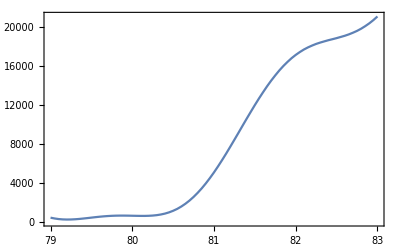

```mathematica
ListLinePlot[tk09s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk09sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/15,0]},{x,79,83,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -15885.7-41728.1 ⅈ and 3070.88 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 18043.3-5153.97 ⅈ and 1765.74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 31490.3-26520.5 ⅈ and 2909.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 9229.28+16763.5 ⅈ and 1649.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 32459.2+18771. ⅈ and 2800.22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -14861.8+12891.8 ⅈ and 1540.17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.09661×10^7}. NIntegrate obtained 34120.7+8894.84 ⅈ and 1080.12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4628×10^7}. NIntegrate obtained 80585.2-1004.6 ⅈ and 1083.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.5299×10^7}. NIntegrate obtained 2247.07+38367.1 ⅈ and 1050.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4628×10^7}. NIntegrate obtained 31961.+80234.3 ⅈ and 1132.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.30088×10^7}. NIntegrate obtained -38928.5+15442.1 ⅈ and 1030.41 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.01119×10^6}. NIntegrate obtained -67715.6+63153.1 ⅈ and 1199.95 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained 116214.-90415.3 ⅈ and 2096.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.59062×10^7}. NIntegrate obtained 31014.9-212121. ⅈ and 2946.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.59062×10^7}. NIntegrate obtained 213751.-53770.6 ⅈ and 3065.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained 133885.+76910. ⅈ and 2188.85 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.28553×10^6}. NIntegrate obtained 134812.+181731. ⅈ and 3171.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.14347×10^7}. NIntegrate obtained -21268.+159956. ⅈ and 2273.69 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.18582×10^7}. NIntegrate obtained -154165.-217065. ⅈ and 4007.31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.43244×10^7}. NIntegrate obtained -295967.-71630.1 ⅈ and 4873.94 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.13637×10^6}. NIntegrate obtained 144939.-228500. ⅈ and 4090.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.43244×10^7}. NIntegrate obtained -44706.8-304852. ⅈ and 4954.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.058×10^7}. NIntegrate obtained 270407.+48546.9 ⅈ and 4186.52 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.43244×10^7}. NIntegrate obtained 269163.-157167. ⅈ and 5041.18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(79. | 682.646
79.05 | 840.32
79.1 | 1010.02
79.15 | 1182.34
79.2 | 1361.42
79.25 | 1538.44
79.3 | 1713.35
79.35 | 1882.7
79.4 | 2036.43
79.45 | 2184.05
79.5 | 2313.54
79.55 | 2425.44
79.6 | 2518.03
79.65 | 2590.32
79.7 | 2639.7
79.75 | 2669.12
79.8 | 2674.08
79.85 | 2659.3
79.9 | 2624.66
79.95 | 2568.
80. | 2493.55
80.05 | 2404.07
80.1 | 2298.56
80.15 | 2182.32
80.2 | 2056.
80.25 | 1922.35
80.3 | 1782.26
80.35 | 1641.06
80.4 | 1498.25
80.45 | 1357.56
80.5 | 1218.28
80.55 | 1087.13
80.6 | 957.613
80.65 | 837.771
80.7 | 726.183
80.75 | 622.568
80.8 | 529.092
80.85 | 443.928
80.9 | 369.074
80.95 | 301.297
81. | 244.518
81.05 | 192.975
81.1 | 150.725
81.15 | 114.992
81.2 | 85.5614
81.25 | 62.5052
81.3 | 45.4303
81.35 | 33.0142
81.4 | 26.2891
81.45 | 25.2425
81.5 | 29.7504
81.55 | 40.2647
81.6 | 57.4947
81.65 | 81.8328
81.7 | 114.677
81.75 | 155.533
81.8 | 208.585
81.85 | 271.715
81.9 | 347.208
81.95 | 436.641
82. | 539.735
82.05 | 658.063
82.1 | 793.165
82.15 | 943.209
82.2 | 1109.92
82.25 | 1293.18
82.3 | 1491.78
82.35 | 1705.96
82.4 | 1935.4
82.45 | 2175.5
82.5 | 2428.5
82.55 | 2688.91
82.6 | 2956.1
82.65 | 3226.65
82.7 | 3500.1
82.75 | 3768.68
82.8 | 4033.29
82.85 | 4288.73
82.9 | 4531.09
82.95 | 4759.58
83. | 4971.41)

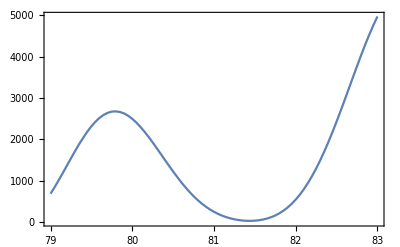

```mathematica
ListLinePlot[tk09sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll2ts1=AmplTwistTab[1,84.2/mee,84.2/mee/15];
ll2tsm1=AmplTwistTab[-1,84.2/mee,84.2/mee/15];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -69587.1+893555. ⅈ and 7086.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 907615.+58837.3 ⅈ and 7105.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 19637.+896232. ⅈ and 7090.04 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 910178.-30239.7 ⅈ and 7103.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.25479×10^7}. NIntegrate obtained 108695.+890157. ⅈ and 7090.72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34774×10^7}. NIntegrate obtained 903999.-119150. ⅈ and 7101.86 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained 74272.9-916747. ⅈ and 6914.22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained -902872.-84940.3 ⅈ and 7093.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.43057×10^7}. NIntegrate obtained -14672.1-919452. ⅈ and 6917.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.76754×10^6}. NIntegrate obtained -905703.+4150.96 ⅈ and 7089.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.01565×10^7}. NIntegrate obtained -103477.-913447. ⅈ and 6927.29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1086×10^7}. NIntegrate obtained -899776.+93127.2 ⅈ and 7091.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -69587.1+893555. ⅈ and 7086.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 907615.+58837.3 ⅈ and 7105.47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 19637.+896232. ⅈ and 7090.04 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained 910178.-30239.7 ⅈ and 7103.61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.25479×10^7}. NIntegrate obtained 108695.+890157. ⅈ and 7090.72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.34774×10^7}. NIntegrate obtained 903999.-119150. ⅈ and 7101.86 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained 74272.9-916747. ⅈ and 6914.22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.5134×10^7}. NIntegrate obtained -902872.-84940.3 ⅈ and 7093.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.43057×10^7}. NIntegrate obtained -14672.1-919452. ⅈ and 6917.19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.76754×10^6}. NIntegrate obtained -905703.+4150.96 ⅈ and 7089.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.01565×10^7}. NIntegrate obtained -103477.-913447. ⅈ and 6927.29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1086×10^7}. NIntegrate obtained -899776.+93127.2 ⅈ and 7091.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 46299.3-424326. ⅈ and 7148.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4122×10^7}. NIntegrate obtained 49512.2-423157. ⅈ and 7327.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 46038.6-424702. ⅈ and 7157.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained 49453.9-422872. ⅈ and 7307.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.68544×10^7}. NIntegrate obtained 45803.5-425070. ⅈ and 7142.93 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.0074×10^7}. NIntegrate obtained 49396.-422657. ⅈ and 7306.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.19968×10^7}. NIntegrate obtained 43996.4-430679. ⅈ and 7226.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.32937×10^7}. NIntegrate obtained 46912.7-429969. ⅈ and 7065.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.19968×10^7}. NIntegrate obtained 43990.7-430922. ⅈ and 7200.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.32937×10^7}. NIntegrate obtained 47222.8-429561. ⅈ and 7087.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.79489×10^7}. NIntegrate obtained 44064.-431121. ⅈ and 7211.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 47532.6-429127. ⅈ and 7083.02 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.4122×10^7}. NIntegrate obtained 49512.2-423157. ⅈ and 7327.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 46299.3-424326. ⅈ and 7148.48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.43882×10^7}. NIntegrate obtained 49453.9-422872. ⅈ and 7307.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.09023×10^7}. NIntegrate obtained 46038.6-424702. ⅈ and 7157.71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.0074×10^7}. NIntegrate obtained 49396.-422657. ⅈ and 7306.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.68544×10^7}. NIntegrate obtained 45803.5-425070. ⅈ and 7142.93 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.19968×10^7}. NIntegrate obtained 43996.4-430679. ⅈ and 7226.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.32937×10^7}. NIntegrate obtained 46912.7-429969. ⅈ and 7065.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.19968×10^7}. NIntegrate obtained 43990.7-430922. ⅈ and 7200.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.32937×10^7}. NIntegrate obtained 47222.8-429561. ⅈ and 7087.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.79489×10^7}. NIntegrate obtained 44064.-431121. ⅈ and 7211.09 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.87772×10^7}. NIntegrate obtained 47532.6-429127. ⅈ and 7083.02 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
```

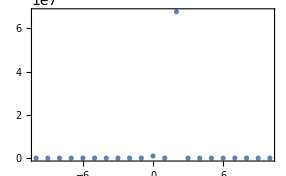
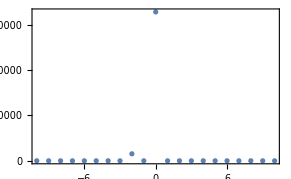

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*старое*)
```

```mathematica
tk03s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,26,34,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -416117.-52056.2 ⅈ and 4173.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 97043.9-29399.5 ⅈ and 3192.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.25479×10^7}. NIntegrate obtained -140528.-435433. ⅈ and 4287.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.6697×10^7}. NIntegrate obtained 50373.6+65370.4 ⅈ and 3248.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 350502.-341851. ⅈ and 4355.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -25618.8+59683.6 ⅈ and 3307.62 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -277787.+260972. ⅈ and 5419.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.6697×10^7}. NIntegrate obtained -320123.-109580. ⅈ and 5499.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 46543.3-716314. ⅈ and 6872.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 746778.-312386. ⅈ and 6984.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -41069.9-279372. ⅈ and 5580.66 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 672854.+586084. ⅈ and 7086.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -1.40737×10^6-1.43795×10^6 ⅈ and 8665.13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -2.3257×10^6-37406.2 ⅈ and 10603.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 717557.-1.93022×10^6 ⅈ and 8791.65 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -955144.-2.10762×10^6 ⅈ and 10967.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 2.10388×10^6-170406. ⅈ and 8920.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1.47752×10^6-1.75238×10^6 ⅈ and 11124.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -1.01094×10^6+977840. ⅈ and 12884.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -8288.04+73202.9 ⅈ and 16438.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -1.23151×10^6-456455. ⅈ and 13570.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -14054.-13628.6 ⅈ and 16640.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -105266.-1.21324×10^6 ⅈ and 13526.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 51163.7+10639.4 ⅈ and 16843.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -350096.-356270. ⅈ and 19926.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 180141.-462164. ⅈ and 20143. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -222430.-35906.7 ⅈ and 24124.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.93656×10^7}. NIntegrate obtained 498399.-22619.5 ⅈ and 20324.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -56742.3-196110. ⅈ and 24368.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.69182×10^7}. NIntegrate obtained 126620.-121096. ⅈ and 24671. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 133.953
26.05 | 5.32666
26.1 | 235.18
26.15 | 649.163
26.2 | 1009.59
26.25 | 1102.6
26.3 | 885.329
26.35 | 469.563
26.4 | 99.4682
26.45 | 30.4952
26.5 | 381.665
26.55 | 1025.12
26.6 | 1605.33
26.65 | 1733.08
26.7 | 1299.59
26.75 | 608.309
26.8 | 223.968
26.85 | 563.506
26.9 | 1557.15
26.95 | 2540.3
27. | 2833.08
27.05 | 2224.19
27.1 | 1190.77
27.15 | 597.342
27.2 | 983.205
27.25 | 2104.86
27.3 | 3125.64
27.35 | 3264.55
27.4 | 2400.39
27.45 | 1195.32
27.5 | 516.237
27.55 | 757.688
27.6 | 1575.
27.65 | 2209.93
27.7 | 2125.23
27.75 | 1408.45
27.8 | 571.508
27.85 | 82.1209
27.9 | 47.4852
27.95 | 268.534
28. | 550.633
28.05 | 872.761
28.1 | 1258.41
28.15 | 1543.78
28.2 | 1473.05
28.25 | 1041.2
28.3 | 750.725
28.35 | 1388.18
28.4 | 3313.13
28.45 | 5907.19
28.5 | 7767.07
28.55 | 8036.14
28.6 | 7092.94
28.65 | 6759.24
28.7 | 8860.95
28.75 | 13491.4
28.8 | 18704.5
28.85 | 21902.2
28.9 | 21880.4
28.95 | 20314.1
29. | 20546.3
29.05 | 24732.8
29.1 | 31996.6
29.15 | 38757.9
29.2 | 41358.2
29.25 | 39561.4
29.3 | 36827.
29.35 | 37456.5
29.4 | 43324.5
29.45 | 51896.2
29.5 | 57935.9
29.55 | 58281.
29.6 | 54336.
29.65 | 50762.3
29.7 | 52182.1
29.75 | 58976.6
29.8 | 66577.4
29.85 | 69619.5
29.9 | 66170.
29.95 | 59059.6
30. | 54175.
30.05 | 55136.5
30.1 | 60637.7
30.15 | 65026.5
30.2 | 63860.1
30.25 | 56911.7
30.3 | 48689.7
30.35 | 44601.9
30.4 | 46055.3
30.45 | 49953.5
30.5 | 51142.2
30.55 | 46876.1
30.6 | 38721.5
30.65 | 31537.7
30.7 | 28565.7
30.75 | 29581.9
30.8 | 31159.9
30.85 | 29686.2
30.9 | 24231.7
30.95 | 17626.8
31. | 12990.4
31.05 | 11903.2
31.1 | 12940.8
31.15 | 13176.2
31.2 | 10994.4
31.25 | 7206.39
31.3 | 3862.67
31.35 | 2487.67
31.4 | 2797.57
31.45 | 3290.51
31.5 | 2821.05
31.55 | 1477.86
31.6 | 292.701
31.65 | 55.893
31.7 | 556.063
31.75 | 933.16
31.8 | 678.789
31.85 | 189.158
31.9 | 303.041
31.95 | 1361.31
32. | 2702.4
32.05 | 3273.51
32.1 | 2705.56
32.15 | 1753.93
32.2 | 1628.07
32.25 | 2913.48
32.3 | 4823.25
32.35 | 5934.45
32.4 | 5402.44
32.45 | 3802.23
32.5 | 2622.04
32.55 | 2943.85
32.6 | 4529.89
32.65 | 5922.47
32.7 | 5873.78
32.75 | 4343.84
32.8 | 2550.52
32.85 | 1856.33
32.9 | 2593.08
32.95 | 3788.05
33. | 4161.16
33.05 | 3246.5
33.1 | 1713.84
33.15 | 696.731
33.2 | 749.289
33.25 | 1435.57
33.3 | 1842.19
33.35 | 1473.
33.4 | 633.363
33.45 | 57.6273
33.5 | 146.666
33.55 | 606.312
33.6 | 822.506
33.65 | 535.653
33.7 | 94.507
33.75 | 78.6934
33.8 | 648.82
33.85 | 1335.07
33.9 | 1503.58
33.95 | 1015.26
34. | 416.821)

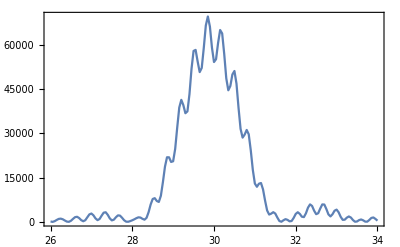

```mathematica
ListLinePlot[tk03s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,26,34,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 648953.+46185.4 ⅈ and 4507.92 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -181827.+32983.5 ⅈ and 3426.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 248918.+626370. ⅈ and 4579.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -79861.-103919. ⅈ and 3482.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -475351.+503956. ⅈ and 4652.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 36255.6-64389.9 ⅈ and 3539.49 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 389838.-338616. ⅈ and 5776.18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 418511.+194482. ⅈ and 5865.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -18225.2+988278. ⅈ and 7329.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -2374.36+406822. ⅈ and 5955.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -1.01289×10^6+445505. ⅈ and 7437.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -926328.-815148. ⅈ and 7546.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 1.90407×10^6+2.01071×10^6 ⅈ and 9210.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1.03015×10^6+2.66305×10^6 ⅈ and 9340.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2.92037×10^6+222886. ⅈ and 9471.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3.16265×10^6+52957.4 ⅈ and 11473.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 1.28745×10^6+2.83635×10^6 ⅈ and 11627. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -1.98241×10^6+2.33235×10^6 ⅈ and 11781.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1.31806×10^6-1.27211×10^6 ⅈ and 14163.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 1.60919×10^6+615859. ⅈ and 14344.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 122731.+1.61217×10^6 ⅈ and 14529.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1692.34-118595. ⅈ and 17348.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 25649.5-26104.4 ⅈ and 17567.3 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -27696.7-49504.7 ⅈ and 17776.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 429760.+483890. ⅈ and 21043.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 286863.+404.66 ⅈ and 25394.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -250583.+606968. ⅈ and 21312.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 102293.+215314. ⅈ and 25695.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -126972.+147249. ⅈ and 25988.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -652924.+40545.6 ⅈ and 21576.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 1101.26
26.05 | 339.597
26.1 | 11.6587
26.15 | 228.135
26.2 | 556.509
26.25 | 532.235
26.3 | 217.974
26.35 | 167.676
26.4 | 822.442
26.45 | 1982.09
26.5 | 2893.99
26.55 | 2972.68
26.6 | 2447.48
26.65 | 2247.1
26.7 | 3194.43
26.75 | 5217.3
26.8 | 7043.69
26.85 | 7665.08
26.9 | 6862.25
26.95 | 5687.91
27. | 5596.79
27.05 | 7110.93
27.1 | 9276.04
27.15 | 10491.1
27.2 | 9847.71
27.25 | 7904.57
27.3 | 6255.03
27.35 | 6104.55
27.4 | 7249.02
27.45 | 8326.87
27.5 | 8007.02
27.55 | 6147.72
27.6 | 3875.87
27.65 | 2494.2
27.7 | 2378.78
27.75 | 2780.01
27.8 | 2650.65
27.85 | 1682.19
27.9 | 529.781
27.95 | 15.1924
28. | 288.653
28.05 | 749.291
28.1 | 821.142
28.15 | 732.475
28.2 | 1405.5
28.25 | 3511.04
28.3 | 6591.46
28.35 | 9290.37
28.4 | 10632.8
28.45 | 11131.3
28.5 | 12671.2
28.55 | 16914.9
28.6 | 23550.6
28.65 | 30298.1
28.7 | 34715.5
28.75 | 36327.6
28.8 | 37485.6
28.85 | 41552.6
28.9 | 49824.1
28.95 | 60191.6
29. | 68521.2
29.05 | 71945.3
29.1 | 71730.9
29.15 | 72346.6
29.2 | 77583.9
29.25 | 87340.3
29.3 | 97325.1
29.35 | 102540.
29.4 | 101855.
29.45 | 98797.8
29.5 | 98515.1
29.55 | 103790.
29.6 | 112515.
29.65 | 119289.
29.7 | 120037.
29.75 | 115021.
29.8 | 108547.
29.85 | 105894.
29.9 | 108776.
29.95 | 113713.
30. | 115044.
30.05 | 109578.
30.1 | 99379.2
30.15 | 90269.4
30.2 | 86668.8
30.25 | 87955.2
30.3 | 89398.8
30.35 | 86284.8
30.4 | 77810.7
30.45 | 67524.7
30.5 | 59948.6
30.55 | 56959.1
30.6 | 56734.1
30.65 | 55324.4
30.7 | 50608.9
30.75 | 42362.5
30.8 | 33957.1
30.85 | 28340.1
30.9 | 26249.8
30.95 | 25775.8
31. | 24145.5
31.05 | 20072.2
31.1 | 14636.6
31.15 | 10061.9
31.2 | 7735.29
31.25 | 7263.29
31.3 | 7135.11
31.35 | 6128.82
31.4 | 4192.33
31.45 | 2155.63
31.5 | 827.566
31.55 | 369.979
31.6 | 379.666
31.65 | 418.684
31.7 | 399.142
31.75 | 493.554
31.8 | 759.561
31.85 | 981.225
31.9 | 904.276
31.95 | 636.206
32. | 609.985
32.05 | 1220.86
32.1 | 2351.66
32.15 | 3335.24
32.2 | 3560.27
32.25 | 2959.42
32.3 | 2162.77
32.35 | 1985.01
32.4 | 2728.32
32.45 | 3891.12
32.5 | 4590.92
32.55 | 4252.5
32.6 | 3112.68
32.65 | 2055.43
32.7 | 1837.09
32.75 | 2475.48
32.8 | 3281.06
32.85 | 3456.15
32.9 | 2764.68
32.95 | 1673.56
33. | 896.465
33.05 | 807.547
33.1 | 1214.63
33.15 | 1594.03
33.2 | 1549.58
33.25 | 1079.57
33.3 | 492.604
33.35 | 115.579
33.4 | 58.4514
33.45 | 204.325
33.5 | 375.478
33.55 | 473.359
33.6 | 486.085
33.65 | 426.417
33.7 | 283.069
33.75 | 109.322
33.8 | 15.5554
33.85 | 136.801
33.9 | 479.817
33.95 | 867.087
34. | 1037.22)

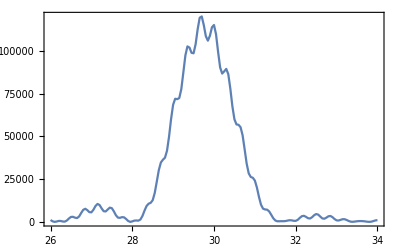

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
llt2s1=AmplTwistTab[1,29.8/mee,29.8/mee/5];
llt2sm1=AmplTwistTab[-1,29.8/mee,29.8/mee/5];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.54002×10^7}. NIntegrate obtained -1.93208×10^6-1.42899×10^6 ⅈ and 10349.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -1.90331×10^6-1.45677×10^6 ⅈ and 10116.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained -1.93266×10^6-1.42977×10^6 ⅈ and 10376.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -1.90562×10^6-1.45356×10^6 ⅈ and 10119.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.30539×10^7}. NIntegrate obtained -1.93304×10^6-1.43089×10^6 ⅈ and 10403.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -1.90794×10^6-1.45042×10^6 ⅈ and 10122.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained -1.91614×10^6-1.47065×10^6 ⅈ and 10575.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained -1.88429×10^6-1.49616×10^6 ⅈ and 10356.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained -1.91369×10^6-1.47398×10^6 ⅈ and 10570.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88385×10^6-1.49527×10^6 ⅈ and 10329. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.18582×10^7}. NIntegrate obtained -1.91117×10^6-1.47717×10^6 ⅈ and 10568. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88367×10^6-1.49409×10^6 ⅈ and 10301.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -1.90331×10^6-1.45677×10^6 ⅈ and 10116.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.54002×10^7}. NIntegrate obtained -1.93208×10^6-1.42899×10^6 ⅈ and 10349.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -1.90562×10^6-1.45355×10^6 ⅈ and 10119.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained -1.93267×10^6-1.42977×10^6 ⅈ and 10376.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -1.90794×10^6-1.45041×10^6 ⅈ and 10122.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.30539×10^7}. NIntegrate obtained -1.93304×10^6-1.4309×10^6 ⅈ and 10403.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained -1.91615×10^6-1.47066×10^6 ⅈ and 10575.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained -1.9137×10^6-1.47398×10^6 ⅈ and 10570.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained -1.88429×10^6-1.49617×10^6 ⅈ and 10356.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.18582×10^7}. NIntegrate obtained -1.91118×10^6-1.47718×10^6 ⅈ and 10568. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88385×10^6-1.49528×10^6 ⅈ and 10329. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88367×10^6-1.49409×10^6 ⅈ and 10301.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -1.97853×10^6+2.5427×10^6 ⅈ and 10925.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.56317×10^6+1.97293×10^6 ⅈ and 10716.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -2.21714×10^6+2.33556×10^6 ⅈ and 10950. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.35632×10^6+2.21593×10^6 ⅈ and 10722.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.03963×10^7}. NIntegrate obtained -2.43409×10^6+2.10625×10^6 ⅈ and 10970.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1592×10^7}. NIntegrate obtained 2.12646×10^6+2.43726×10^6 ⅈ and 10726.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.21805×10^7}. NIntegrate obtained -2.54118×10^6-1.95303×10^6 ⅈ and 11125. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained 1.94849×10^6-2.563×10^6 ⅈ and 10926.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.80313×10^7}. NIntegrate obtained -2.33875×10^6-2.19134×10^6 ⅈ and 11128.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 2.19151×10^6-2.36054×10^6 ⅈ and 10910.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -2.11416×10^6-2.40892×10^6 ⅈ and 11126.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.86385×10^7}. NIntegrate obtained 2.4137×10^6-2.13497×10^6 ⅈ and 10890.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.56317×10^6+1.97293×10^6 ⅈ and 10716.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.35632×10^6+2.21593×10^6 ⅈ and 10722.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -1.97854×10^6+2.54271×10^6 ⅈ and 10925.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1592×10^7}. NIntegrate obtained 2.12646×10^6+2.43727×10^6 ⅈ and 10726.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -2.21715×10^6+2.33556×10^6 ⅈ and 10950. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.03963×10^7}. NIntegrate obtained -2.43409×10^6+2.10625×10^6 ⅈ and 10970.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.21805×10^7}. NIntegrate obtained -2.54119×10^6-1.95304×10^6 ⅈ and 11125. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.80313×10^7}. NIntegrate obtained -2.33876×10^6-2.19134×10^6 ⅈ and 11128.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained 1.94849×10^6-2.56301×10^6 ⅈ and 10926.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -2.11416×10^6-2.40893×10^6 ⅈ and 11126.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 2.19152×10^6-2.36054×10^6 ⅈ and 10910.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.86385×10^7}. NIntegrate obtained 2.4137×10^6-2.13497×10^6 ⅈ and 10890.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tm2s1=Table[{m,dProbabTwist[m,llt2s1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,llt2sm1[[3]]]},{m,-mMax,mMax}];
```

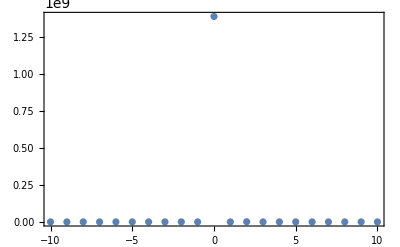
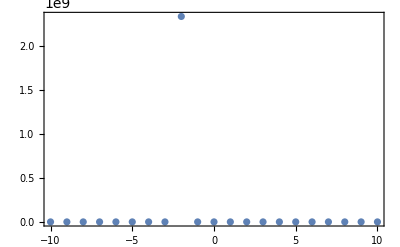

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk0=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}](*ТВ не работает в окрестности щели*)
tk0m1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}]
```

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

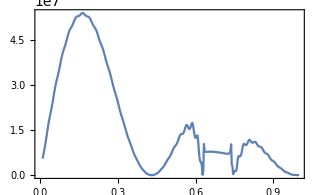
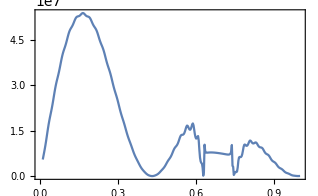

```mathematica
{ListLinePlot[tk0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0m1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk02=ParallelTable[{x,dProbabPlane[1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 332.434+464.367 ⅈ and 0.0225361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -619.429-681.286 ⅈ and 0.0489122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1166.92-1085.18 ⅈ and 0.0531897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1049.87+942.244 ⅈ and 0.0246899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained 1403.62+442.504 ⅈ and 0.0574778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -1526.59-450.397 ⅈ and 0.0268764 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1065.22+1179.94 ⅈ and 0.100125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1599.05-1893.63 ⅈ and 0.194516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -1491.3+1330.95 ⅈ and 0.107954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 1990.87-1471.91 ⅈ and 0.207805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -1175.98-619.844 ⅈ and 0.115856 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained 626.425+1054.45 ⅈ and 0.221913 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1982.27+2680.07 ⅈ and 0.3599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -2612.04+1173.71 ⅈ and 0.380563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1832.02-3256.02 ⅈ and 0.645988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 486.128-1763.34 ⅈ and 0.407687 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3217.53-123.066 ⅈ and 0.684446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -2250.62+2568.21 ⅈ and 0.718666 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 881.154+3162.89 ⅈ and 1.09986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 485.005-1726.07 ⅈ and 1.82392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3491.98-1628.25 ⅈ and 1.16148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 2866.23+3254.44 ⅈ and 1.92718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 4385.48-2971.69 ⅈ and 1.23135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -6145.54+2217.64 ⅈ and 2.03664 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 304719.
11.1 | 279461.
11.2 | 1.31877×10^6
11.3 | 512705.
11.4 | 125542.
11.5 | 1.01398×10^6
11.6 | 416903.
11.7 | 173895.
11.8 | 936334.
11.9 | 281377.
12. | 264000.
12.1 | 1.20874×10^6
12.2 | 428952.
12.3 | 153690.
12.4 | 998279.
12.5 | 366183.
12.6 | 177109.
12.7 | 838245.
12.8 | 195352.
12.9 | 324498.
13. | 1.08877×10^6
13.1 | 259790.
13.2 | 268007.
13.3 | 1.01484×10^6
13.4 | 257273.
13.5 | 231225.
13.6 | 759894.
13.7 | 106837.
13.8 | 419600.
13.9 | 896155.
14. | 81479.1
14.1 | 473734.
14.2 | 965980.
14.3 | 106007.
14.4 | 373409.
14.5 | 703267.
14.6 | 47134.5
14.7 | 501737.
14.8 | 627169.
14.9 | 2871.81
15. | 697104.
15.1 | 745254.
15.2 | 2059.48
15.3 | 621357.
15.4 | 606349.
15.5 | 18001.3
15.6 | 571041.
15.7 | 376450.
15.8 | 70299.5
15.9 | 774838.
16. | 372218.
16.1 | 92284.6
16.2 | 847623.
16.3 | 370166.
16.4 | 87105.5
16.5 | 674905.
16.6 | 203127.
16.7 | 197535.
16.8 | 649360.
16.9 | 80018.6
17. | 359298.
17.1 | 784258.
17.2 | 72759.6
17.3 | 372615.
17.4 | 709122.
17.5 | 48947.9
17.6 | 362860.
17.7 | 486773.
17.8 | 16706.1
17.9 | 531841.
18. | 426198.)

```mathematica
tk02m=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -2793.18-2204.31 ⅈ and 0.026092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 3256.52+2176.42 ⅈ and 0.0561108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1670.05-390.341 ⅈ and 0.0285185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -2077.26+685.351 ⅈ and 0.0608922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -819.237+326.726 ⅈ and 0.0310953 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 815.52-928.859 ⅈ and 0.0659392 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -3756.17-2516.07 ⅈ and 0.113817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 4097.79+3301.84 ⅈ and 0.219223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 2956.87-929.56 ⅈ and 0.122666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -4342.25+962.25 ⅈ and 0.234918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 1279.86-3545.97 ⅈ and 0.251625 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -904.662+2029.06 ⅈ and 0.132053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3958.68-4523.45 ⅈ and 0.403549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 6093.56-511.573 ⅈ and 0.430082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3037.49+5829.4 ⅈ and 0.714869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2269.15+5181.93 ⅈ and 0.459151 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -7685.83-669.5 ⅈ and 0.759424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 4180.56-6312.13 ⅈ and 0.805781 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1371.15-6280. ⅈ and 1.21921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 8153.14+2501.23 ⅈ and 1.29087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -6956.76+6097.76 ⅈ and 1.36669 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -191.227+4281.74 ⅈ and 2.01614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -6354.05-4108.33 ⅈ and 2.12821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 9762.51-3843.13 ⅈ and 2.24587 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 387536.
11.1 | 28098.2
11.2 | 319086.
11.3 | 78167.2
11.4 | 194749.
11.5 | 709389.
11.6 | 328555.
11.7 | 254926.
11.8 | 788069.
11.9 | 379902.
12. | 35145.
12.1 | 335693.
12.2 | 84567.3
12.3 | 163096.
12.4 | 598772.
12.5 | 222810.
12.6 | 279197.
12.7 | 796181.
12.8 | 328316.
12.9 | 77245.8
13. | 393225.
13.1 | 86806.4
13.2 | 146631.
13.3 | 456256.
13.4 | 95411.9
13.5 | 349827.
13.6 | 759504.
13.7 | 218387.
13.8 | 191149.
13.9 | 491611.
14. | 79505.9
14.1 | 144551.
14.2 | 320689.
14.3 | 15956.2
14.4 | 413883.
14.5 | 590988.
14.6 | 96989.
14.7 | 396826.
14.8 | 550714.
14.9 | 45319.5
15. | 205958.
15.1 | 255386.
15.2 | 4762.63
15.3 | 396870.
15.4 | 317048.
15.5 | 71538.6
15.6 | 588974.
15.7 | 437414.
15.8 | 43200.1
15.9 | 391899.
16. | 239129.
16.1 | 20303.7
16.2 | 324017.
16.3 | 101075.
16.4 | 152494.
16.5 | 569319.
16.6 | 179973.
16.7 | 193917.
16.8 | 574957.
16.9 | 150235.
17. | 107514.
17.1 | 329608.
17.2 | 24089.
17.3 | 212114.
17.4 | 339062.
17.5 | 22360.5
17.6 | 408569.
17.7 | 482032.
17.8 | 41149.2
17.9 | 361276.
18. | 358150.)

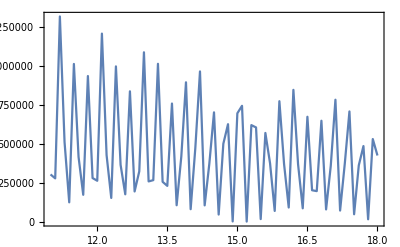
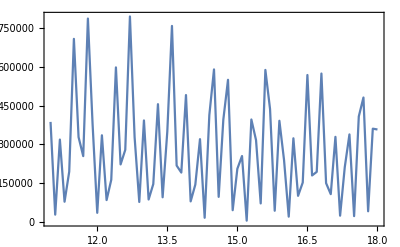

```mathematica
{ListLinePlot[tk02,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk02m,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ParallelTable[dProbabPlane[1,x/mee,1/γ,1/γ],{x,1,2,0.05}]//AbsoluteTiming
```

{16.6569,{6.32595×10^6,8.04833×10^6,7.60734×10^6,5.34935×10^6,2.45492×10^6,385906.,156093.,1.72039×10^6,4.04096×10^6,5.75948×10^6,5.92241×10^6,4.44712×10^6,2.18014×10^6,407201.,79109.,1.29921×10^6,3.31154×10^6,4.9242×10^6,5.19799×10^6,4.00629×10^6,2.06202×10^6}}

```mathematica
(*старое*)
```